# Casas-Ibarra Parametrization

## Info

This method uses the Casas-Ibarra parametrization to transform the constrains and measurements on neutrino observables like mass splitting and mixing angles into constrains on the couplings of the model.

arXiv : hep - ph/010365

Procedure

GENERAL PROCEDURE:

We factorize the couplings in the equation for the neutrino masses in a specific model:
M_ν = λᵀ M λ
The matrix M can be further diagonalized with a rotation U_M:
M_ν = λᵀ M λ = λᵀ U_M†D_M U_M λ
This mass matrix can be diagonalized using the PMNS matrix:
diag(m_ν1, m_ν2, m_ν3) = D_ν = U_PMNS†M_ν U_PMNS = U_PMNS†λᵀ M λ U_PMNS = U_PMNS† λᵀ U_M†D_M U_M λ U_PMNS
Multiplying both sides by D_ν^(-1/2)
Id = diag(1,1,1) = D_ν^(-1/2)U_PMNS† λᵀ U_M†D_M U_M λ U_PMNS D_ν^(-1/2) = (D_ν^(-1/2)U_PMNS† λᵀ U_M†D_M^(1/2))(D_M^(1/2)U_M λ U_PMNS D_ν^(-1/2))
The two terms can be parametrized with a rotation matrix, since their product gives the Identity matrix:
R =D_M^(1/2)U_M λ U_PMNS D_ν^(-1/2)
Id = R†R
The rotation matrix can be parametrized in a general way using only one parameter, a rotation angle θ.
We can write the couplings as function of this new parametrization:
λ = U_M ᵀ D_M^(-1/2)R D_ν^(1/2) U_PMNS†

INTERPRETATION:

The couplings can be obtained fixing the various other parameter in an unique way and we will obtain a configuration that satisfy the experimental constrains.
The dependencies are:
M is the neutrino mass matrix that is obtained in the specific model. Since the dependencies on the couplings are factorized, this matrix only depends on the BSM masses circulating in the loop diagrams that generate the neutrino masses in the specific model. The model dependencies are all contained in this matrix. This information is then splitted in the following two:
U_M is the rotation matrix that diagonalize the neutrino mass matrix obtained in this model (the matrix M )
D_M is the diagonalized neutrino mass matrix that is obtained in this model (the matrix M )
R is a rotation matrix that can be parametrized with a single parameter θ. Varying this parameter we will obtain the various combination of couplings λ that satisfy the experimental constrains.
D_ν contains the experimental measurements and constrains on the neutrino masses. We can always assume one neutrino masses to be 0, thus the other two are coming directly from the measurements on mass difference (we are fixing the absolute neutrino mass scale).
U_PMNS contains the experimental measurements and constrains on the neutrino mixing.

IN THIS CASE (model T1-3-B-α=0):

In this model the neutrino mass matrix generated from the loop diagrams are diagonal and proportional to the Identity, thus there is no need for diagonalization (U_M = Id), and the diagonalized matrix is proportional to a scalar value D_M = M_0 . Id
The equation for the couplings is then reduced to:
λ = 1/(√M_0)R D_ν^(1/2) U_PMNS†
The dependence on the model parameters (the functions of BSM masses that comes from the loops) are all contained in the matrix M_0

## Input Parameters

SM

```mathematica
v = 2.46220569 10^2;
```

PMNS Matrix

```mathematica
PMNS={{1, 0, 0}, {0, Cos[θ23], Sin[θ23]}, {0, -Sin[θ23], Cos[θ23]}}.{{Cos[θ13], 0, Sin[θ13] ⅇ^(-ⅈ δCP)}, {0, 1, 0}, {-Sin[θ13] ⅇ^(+ⅈ δCP), 0, Cos[θ13]}}.{{Cos[θ12], Sin[θ12], 0}, {-Sin[θ12], Cos[θ12], 0}, {0, 0, 1}};
```

```mathematica
(*PMNS//MatrixForm*)
```

```mathematica
θ12 = 33.62°;
θ12max = θ12+0.78°;
θ12min = θ12-0.76°;
```

```mathematica
θ23 = 47.2°;
θ23max = θ23+1.9°;
θ23min = θ23-3.9°;
```

```mathematica
θ13 = 8.54°;
θ13max = θ13+0.15°;
θ13min = θ13-0.15°;
```

```mathematica
(*δCP = 234°;
δCPmax = δCP+43°;
δCPmin = δCP-31°;*)
```

```mathematica
δCP = 0°;
```

Neutrino mass splitting

```mathematica
m1=0;
```

```mathematica
m2=√(7.53 10^-5);
Δm2 = √2 0.18 10^-5/m2;
```

```mathematica
m3=√(2.44 10^-3+m2^2);
Δm3 = √2 0.06 10^-3/m3;
```

```mathematica
Dnu={{m1, 0, 0}, {0, m2, 0}, {0, 0, m3}}*10^-9;
```

## Model Parameters (Simon)

BSM Couplings

```mathematica
lambda1Input = {{0,0},{0,0}};
```

```mathematica
lambda4Input=5 10^-3;
lambda5Input =5 10^-3;
```

BSM Masses

```mathematica
mCPsiInput=10^3;
mpsipsipInput=1.5 10^3;
```

```mathematica
MPHI2 = {{1.4 10^3,0},{0,3 10^3}}^2;
```

## Model Parameters (test)

BSM Couplings

```mathematica
lambda1Input = {{0,0},{0,0}};
```

```mathematica
lambda4Input=10^-2;
lambda5Input =10^-2;
```

BSM Masses

```mathematica
mCPsiInput=10^2;
mpsipsipInput=10^4;
```

```mathematica
MPHI2 = {{1.4 10^3,0},{0,3 10^3}}^2;
```

## Fermion masses and mixing

Fermion mass matrix

```mathematica
M0 = {{mCPsiInput, (v lambda5Input)/(√2), (v lambda4Input)/(√2)}, {(v lambda5Input)/(√2), 0, mpsipsipInput}, { (v lambda4Input)/(√2), mpsipsipInput, 0}};
```

Eigenvalues and eigenvectors

```mathematica
{eigenM0,UCHI}=Eigensystem[M0];
```

The eigenvector matrix gives the mixing

```mathematica
(*eigenM0*)
```

```mathematica
(*UCHI//MatrixForm*)
```

```mathematica
(*UCHI.M0.UCHIᵀ//MatrixForm*)
```

```mathematica
(*UCHI*.M0.UCHI†//MatrixForm*)
```

## Neutrino Masses

Masses from Loop

```mathematica
Mη2=MPHI2+v^2 lambda1Input;
```

```mathematica
M0nu=DiagonalMatrix[1/(32 π^2)Table[Sum[(UCHI⟦k,3⟧*)^2 (eigenM0⟦k⟧^3/(Mη2⟦l,l⟧-eigenM0⟦k⟧^2))Log[eigenM0⟦k⟧^2/Mη2⟦l,l⟧],{k,1,3}],{l,1,2}]];
```

```mathematica
M0numinusonehalf=DiagonalMatrix[1/√Abs[1/(32 π^2)Table[Sum[(UCHI⟦k,3⟧*)^2 (eigenM0⟦k⟧^3/(Mη2⟦l,l⟧-eigenM0⟦k⟧^2))Log[eigenM0⟦k⟧^2/Mη2⟦l,l⟧],{k,1,3}],{l,1,2}]]];
```

```mathematica
(*M0numinusonehalf=DiagonalMatrix[1/√(1/(32 π^2)Table[Sum[(UCHI⟦k,3⟧*)^2 (eigenM0⟦k⟧^3/(MPHI2⟦l,l⟧-eigenM0⟦k⟧^2))Log[eigenM0⟦k⟧^2/MPHI2⟦l,l⟧],{k,1,3}],{l,1,2}])];*)
```

```mathematica
M0nu//MatrixForm
```

(-9.21511×10^-12 | 0.
0. | -9.21511×10^-12)

```mathematica
M0numinusonehalf//MatrixForm
```

(329420. | 0.
0. | 329420.)

```mathematica
(*{eigenM0,UCHI}*)
```

```mathematica
(*(UCHI⟦;;,3⟧*)^2*)
```

```mathematica
(* (eigenM0⟦;;⟧^3/(MPHI2⟦1,1⟧-eigenM0⟦;;⟧^2))*)
```

```mathematica
(*Log[eigenM0⟦;;⟧^2/MPHI2⟦1,1⟧]*)
```

```mathematica
(*1/(32 π^2)Table[Sum[(UCHI⟦k,3⟧*)^2 (eigenM0⟦k⟧^3/(MPHI2⟦l,l⟧-eigenM0⟦k⟧^2))Log[eigenM0⟦k⟧^2/MPHI2⟦l,l⟧],{k,1,3}],{l,1,2}]*)
```

```mathematica
(*Table[(UCHI⟦k,3⟧*)^2 (eigenM0⟦k⟧^3/(MPHI2⟦1,1⟧-eigenM0⟦k⟧^2))Log[eigenM0⟦k⟧^2/MPHI2⟦1,1⟧],{k,1,3}]*)
```

```mathematica
(*Sum[(UCHI⟦k,3⟧*)^2 (eigenM0⟦k⟧^3/(MPHI2⟦1,1⟧-eigenM0⟦k⟧^2))Log[eigenM0⟦k⟧^2/MPHI2⟦1,1⟧],{k,1,3}]*)
```

Casas-Ibarra Parametrization

```mathematica
ROT[θ_]:={{0, Cos[θ], -Sin[θ]}, {0, Sin[θ], Cos[θ]}};
```

```mathematica
λ[θ_]:=(M0numinusonehalf.ROT[θ].√Dnu.PMNS†)ᵀ//FullSimplify;
```

## Example

Consider one of the possible values for the matrix elements and check if we obtain the correct neutrino masses

```mathematica
λ[θ].λ[θ]ᵀ//FullSimplify//MatrixForm
```

(0.590816 | 1.24386 | 0.292523
1.24386 | 4.56104 | 3.4303
0.292523 | 3.4303 | 4.22306)

```mathematica
λ6Input=λ[0];
```

```mathematica
λ6Input//MatrixForm
```

(0.643873 | 0.419814
0.594387 | 2.05128
-0.784184 | 1.8995)

```mathematica
(PMNS†.(λ6Input.M0nu.λ6Inputᵀ).PMNS)//MatrixForm
```

(-1.13239×10^-28 | -1.70946×10^-27 | 5.57111×10^-27
-1.21169×10^-27 | -8.67756×10^-12 | -6.46235×10^-27
0. | -6.46235×10^-27 | -5.01528×10^-11)

```mathematica
Dnu//MatrixForm
```

(0 | 0 | 0
0 | 8.67756×10^-12 | 0
0 | 0 | 5.01528×10^-11)

Any value of θ would give the same (diagonalized) neutrino mass matrix

```mathematica
(PMNS†.(λ[θ].M0nu.λ[θ]ᵀ).PMNS)//FullSimplify//MatrixForm
```

(3.65171×10^-28-6.37479×10^-28 Cos[2 θ]-7.29242×10^-28 Cos[θ] Sin[θ] | -1.87253×10^-27+9.46995×10^-28 Cos[2 θ]+1.1493×10^-27 Cos[θ] Sin[θ] | 4.87928×10^-27+4.33677×10^-29 Cos[2 θ]-1.9368×10^-28 Cos[θ] Sin[θ]
(1.1493×10^-27 Cos[θ]-1.61559×10^-27 Sin[θ]) Sin[θ] | -8.67756×10^-12-8.07794×10^-28 Cos[2 θ]-1.63371×10^-27 Cos[θ] Sin[θ] | -5.35163×10^-27-2.01948×10^-28 Cos[2 θ]-3.49568×10^-28 Cos[θ] Sin[θ]
-1.9368×10^-28 Cos[θ] Sin[θ] | -6.46235×10^-27-3.49568×10^-28 Cos[θ] Sin[θ] | -5.01528×10^-11+2.36296×10^-27 Cos[θ] Sin[θ])

# Casas-Ibarra Parametrization (with scalar mixing)

## Info

This method uses the Casas-Ibarra parametrization to transform the constrains and measurements on neutrino observables like mass splitting and mixing angles into constrains on the couplings of the model.

arXiv : hep - ph/010365

Procedure

GENERAL PROCEDURE:

We factorize the couplings in the equation for the neutrino masses in a specific model:
M_ν = λᵀ M λ
The matrix M can be further diagonalized with a rotation U_M:
M_ν = λᵀ M λ = λᵀ U_M†D_M U_M λ
This mass matrix can be diagonalized using the PMNS matrix:
diag(m_ν1, m_ν2, m_ν3) = D_ν = U_PMNS†M_ν U_PMNS = U_PMNS†λᵀ M λ U_PMNS = U_PMNS† λᵀ U_M†D_M U_M λ U_PMNS
Multiplying both sides by D_ν^(-1/2)
Id = diag(1,1,1) = D_ν^(-1/2)U_PMNS† λᵀ U_M†D_M U_M λ U_PMNS D_ν^(-1/2) = (D_ν^(-1/2)U_PMNS† λᵀ U_M†D_M^(1/2))(D_M^(1/2)U_M λ U_PMNS D_ν^(-1/2))
The two terms can be parametrized with a rotation matrix, since their product gives the Identity matrix:
R =D_M^(1/2)U_M λ U_PMNS D_ν^(-1/2)
Id = R†R
The rotation matrix can be parametrized in a general way using only one parameter, a rotation angle θ.
We can write the couplings as function of this new parametrization:
λ = U_M ᵀ D_M^(-1/2)R D_ν^(1/2) U_PMNS†

INTERPRETATION:

The couplings can be obtained fixing the various other parameter in an unique way and we will obtain a configuration that satisfy the experimental constrains.
The dependencies are:
M is the neutrino mass matrix that is obtained in the specific model. Since the dependencies on the couplings are factorized, this matrix only depends on the BSM masses circulating in the loop diagrams that generate the neutrino masses in the specific model. The model dependencies are all contained in this matrix. This information is then splitted in the following two:
U_M is the rotation matrix that diagonalize the neutrino mass matrix obtained in this model (the matrix M )
D_M is the diagonalized neutrino mass matrix that is obtained in this model (the matrix M )
R is a rotation matrix that can be parametrized with a single parameter θ. Varying this parameter we will obtain the various combination of couplings λ that satisfy the experimental constrains.
D_ν contains the experimental measurements and constrains on the neutrino masses. We can always assume one neutrino masses to be 0, thus the other two are coming directly from the measurements on mass difference (we are fixing the absolute neutrino mass scale).
U_PMNS contains the experimental measurements and constrains on the neutrino mixing.

IN THIS CASE (model T1-3-B-α=0):

In general in this model the neutrino mass matrix generated from the loop diagrams are diagonal and proportional to the Identity.
This happens because the scalar mass matrix input is diagonal. However here it is included the treatment of the case with non-diagonal scalar mass matrix.
If the scalar mass matrix is diagonal there is no need for diagonalization (U_M = Id), and the diagonalized matrix is proportional to a scalar value D_M = M_0 . Id
The equation for the couplings is then reduced to:
λ = 1/(√M_0)R D_ν^(1/2) U_PMNS†
The dependence on the model parameters (the functions of BSM masses that comes from the loops) are all contained in the matrix M_0

## Input Parameters

SM

```mathematica
v = 2.46220569 10^2;
```

PMNS Matrix

```mathematica
PMNS={{1, 0, 0}, {0, Cos[θ23], Sin[θ23]}, {0, -Sin[θ23], Cos[θ23]}}.{{Cos[θ13], 0, Sin[θ13] ⅇ^(-ⅈ δCP)}, {0, 1, 0}, {-Sin[θ13] ⅇ^(+ⅈ δCP), 0, Cos[θ13]}}.{{Cos[θ12], Sin[θ12], 0}, {-Sin[θ12], Cos[θ12], 0}, {0, 0, 1}};
```

```mathematica
(*PMNS//MatrixForm*)
```

```mathematica
θ12 = 33.62°;
θ12max = θ12+0.78°;
θ12min = θ12-0.76°;
```

```mathematica
θ23 = 47.2°;
θ23max = θ23+1.9°;
θ23min = θ23-3.9°;
```

```mathematica
θ13 = 8.54°;
θ13max = θ13+0.15°;
θ13min = θ13-0.15°;
```

```mathematica
(*δCP = 234°;
δCPmax = δCP+43°;
δCPmin = δCP-31°;*)
```

```mathematica
δCP = 0°;
```

Neutrino mass splitting

```mathematica
m1=0;
```

```mathematica
m2=√(7.53 10^-5);
Δm2 = √2 0.18 10^-5/m2;
```

```mathematica
m3=√(2.44 10^-3+m2^2);
Δm3 = √2 0.06 10^-3/m3;
```

```mathematica
Dnu={{m1, 0, 0}, {0, m2, 0}, {0, 0, m3}}*10^-9;
```

## Model Parameters (Simon)

BSM Couplings

```mathematica
lambda1Input = {{0,0},{0,0}};
```

```mathematica
lambda4Input=5 10^-3;
lambda5Input =5 10^-3;
```

BSM Masses

```mathematica
mCPsiInput=10^3;
mpsipsipInput=1.5 10^3;
```

```mathematica
MPHI2 = {{1.4 10^3,0},{0,3 10^3}}^2;
```

```mathematica
(*MPHI2 = {{1.4 10^3,2.5 10^2},{2.5 10^2,3 10^3}}^2;*)
```

## Model Parameters (test)

BSM Couplings

```mathematica
lambda1Input = {{0,0},{0,0}};
```

```mathematica
lambda4Input=10^-5;
lambda5Input =10^-5;
```

BSM Masses

```mathematica
mCPsiInput=10^3;
mpsipsipInput=1 10^0;
```

```mathematica
MPHI2 = {{1.4 10^3,0},{0,3 10^3}}^2;
```

## Fermion masses and mixing

Fermion mass matrix

```mathematica
M0 = {{mCPsiInput, (v lambda5Input)/(√2), (v lambda4Input)/(√2)}, {(v lambda5Input)/(√2), 0, mpsipsipInput}, { (v lambda4Input)/(√2), mpsipsipInput, 0}};
```

Eigenvalues and eigenvectors

```mathematica
{eigenM0,UCHI}=Eigensystem[M0];
```

The eigenvector matrix gives the mixing

```mathematica
(*eigenM0*)
```

```mathematica
(*UCHI//MatrixForm*)
```

```mathematica
(*UCHI.M0.UCHIᵀ//MatrixForm*)
```

```mathematica
(*UCHI*.M0.UCHI†//MatrixForm*)
```

## Scalar masses and mixing

Eigenvalues and eigenvectors

```mathematica
Mη2=MPHI2+v^2 lambda1Input;
```

```mathematica
{eigenS0,US}=Eigensystem[Mη2];
```

The eigenvector matrix gives the mixing

```mathematica
(*eigenS0*)
```

```mathematica
(*US//MatrixForm*)
```

```mathematica
(*US.MPHI2.USᵀ//MatrixForm*)
```

```mathematica
(*US*.MPHI2.US†//MatrixForm*)
```

## Neutrino Masses

Masses from Loop

```mathematica
M0nu=Table[1/(32 π^2)Sum[US⟦l,i⟧US⟦l,j⟧ Sum[(UCHI⟦k,3⟧*)^2 (eigenM0⟦k⟧^3/(eigenS0⟦l⟧-eigenM0⟦k⟧^2))Log[eigenM0⟦k⟧^2/eigenS0⟦l⟧],{k,1,3}],{l,1,2}],{i,1,2},{j,1,2}];
```

```mathematica
{eigenM0nu,UM}=Eigensystem[M0nu];
```

```mathematica
(*DM = DiagonalMatrix[Abs[eigenM0nu]];*)
```

```mathematica
(*UM.M0nu.UMᵀ//MatrixForm*)
```

```mathematica
DMminusonehalf = DiagonalMatrix[1/√Abs[eigenM0nu]];
```

Casas-Ibarra Parametrization

```mathematica
ROT[θ_]:={{0, Cos[θ], -Sin[θ]}, {0, Sin[θ], Cos[θ]}};
```

```mathematica
λ[θ_]:=(UMᵀ.DMminusonehalf.ROT[θ].√Dnu.PMNS†)ᵀ//FullSimplify;
```

## Example

Consider one of the possible values for the matrix elements and check if we obtain the correct neutrino masses

```mathematica
λ[θ].λ[θ]ᵀ//FullSimplify//MatrixForm
```

(0.97684-0.172188 Cos[2 θ]+0.781163 Cos[θ] Sin[θ] | 2.05657+0.345666 Cos[2 θ]+2.26901 Cos[θ] Sin[θ] | 0.48365+0.940922 Cos[2 θ]+1.29154 Cos[θ] Sin[θ]
2.05657+0.345666 Cos[2 θ]+2.26901 Cos[θ] Sin[θ] | 7.5411+2.78475 Cos[2 θ]+3.52354 Cos[θ] Sin[θ] | 5.67157+3.15183 Cos[2 θ]-0.692911 Cos[θ] Sin[θ]
0.48365+0.940922 Cos[2 θ]+1.29154 Cos[θ] Sin[θ] | 5.67157+3.15183 Cos[2 θ]-0.692911 Cos[θ] Sin[θ] | 6.9823+2.1625 Cos[2 θ]-4.3047 Cos[θ] Sin[θ])

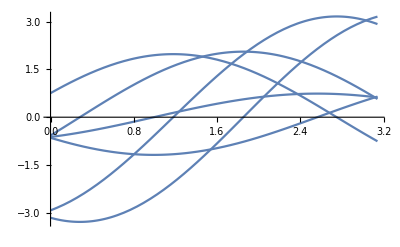

```mathematica
Plot[λ[θ],{θ,0,π}]
```

```mathematica
λ6Input=λ[0];
```

```mathematica
λ6Input//MatrixForm
```

(-0.621228 | -0.647092
-0.573483 | -3.1618
0.756604 | -2.92786)

```mathematica
(PMNS†.(λ6Input.M0nu.λ6Inputᵀ).PMNS)//MatrixForm
```

(-1.12037×10^-28 | 4.79277×10^-28 | 2.93389×10^-27
-1.21169×10^-27 | -8.67756×10^-12 | -5.65455×10^-27
3.23117×10^-27 | -9.69352×10^-27 | -5.01528×10^-11)

```mathematica
Dnu//MatrixForm
```

(0 | 0 | 0
0 | 8.67756×10^-12 | 0
0 | 0 | 5.01528×10^-11)

Any value of θ would give the same (diagonalized) neutrino mass matrix

```mathematica
(PMNS†.(λ[θ].M0nu.λ[θ]ᵀ).PMNS)//FullSimplify//MatrixForm
```

(-3.50649×10^-28+6.37479×10^-28 Cos[2 θ]+2.43081×10^-28 Cos[θ] Sin[θ] | -3.91136×10^-28-9.46995×10^-28 Cos[2 θ]-3.83098×10^-28 Cos[θ] Sin[θ] | 3.38668×10^-27-4.33677×10^-29 Cos[2 θ]+6.45601×10^-29 Cos[θ] Sin[θ]
6.05845×10^-28-1.00974×10^-27 Cos[2 θ]-3.83098×10^-28 Cos[θ] Sin[θ] | -8.67756×10^-12+3.23117×10^-27 Cos[2 θ]+5.44571×10^-28 Cos[θ] Sin[θ] | -4.44286×10^-27-8.07794×10^-28 Cos[2 θ]+1.16523×10^-28 Cos[θ] Sin[θ]
Cos[θ] (3.23117×10^-27 Cos[θ]+6.45601×10^-29 Sin[θ]) | -6.46235×10^-27-3.23117×10^-27 Cos[2 θ]+1.16523×10^-28 Cos[θ] Sin[θ] | -5.01528×10^-11+6.46235×10^-27 Cos[2 θ]-7.87652×10^-28 Cos[θ] Sin[θ])

# Casas-Ibarra Parametrization Function

## Input Parameters

SM

```mathematica
v = 2.46220569 10^2;
```

PMNS Matrix

```mathematica
PMNS={{1, 0, 0}, {0, Cos[θ23], Sin[θ23]}, {0, -Sin[θ23], Cos[θ23]}}.{{Cos[θ13], 0, Sin[θ13] ⅇ^(-ⅈ δCP)}, {0, 1, 0}, {-Sin[θ13] ⅇ^(+ⅈ δCP), 0, Cos[θ13]}}.{{Cos[θ12], Sin[θ12], 0}, {-Sin[θ12], Cos[θ12], 0}, {0, 0, 1}};
```

```mathematica
(*PMNS//MatrixForm*)
```

```mathematica
θ12 = 33.62°;
θ12max = θ12+0.78°;
θ12min = θ12-0.76°;
```

```mathematica
θ23 = 47.2°;
θ23max = θ23+1.9°;
θ23min = θ23-3.9°;
```

```mathematica
θ13 = 8.54°;
θ13max = θ13+0.15°;
θ13min = θ13-0.15°;
```

```mathematica
(*δCP = 234°;
δCPmax = δCP+43°;
δCPmin = δCP-31°;*)
```

```mathematica
δCP = 0°;
```

Neutrino mass splitting

```mathematica
m1=0;
```

```mathematica
m2=√(7.53 10^-5);
Δm2 = √2 0.18 10^-5/m2;
```

```mathematica
m3=√(2.44 10^-3+m2^2);
Δm3 = √2 0.06 10^-3/m3;
```

```mathematica
Dnu={{m1, 0, 0}, {0, m2, 0}, {0, 0, m3}}*10^-9;
```

## Model Parameters (Simon - Table7.3)

BSM Couplings

```mathematica
lambda1Input = {{0,0},{0,0}};
```

```mathematica
lambda4Input=5 10^-3;
lambda5Input =5 10^-3;
```

BSM Masses

```mathematica
mCPsiInput=10^3;
mpsipsipInput=1.5 10^3;
```

```mathematica
MPHI2 = {{1.4 10^3,0},{0,3 10^3}}^2;
```

## Casas-Ibarra Function

```mathematica
CI[λ4_,λ5_,Mψ_,mψψ_,m2ϕ_]:=Block[{λ1,M0,eigenM0,UCHI,eigenS0,US,M0nu,eigenM0nu,UM,DMminusonehalf,ROT,λ6},
λ1 = {{0,0},{0,0}};
M0 = {{Mψ, (v λ5)/(√2), (v λ4)/(√2)}, {(v λ5)/(√2), 0, mψψ}, { (v λ4)/(√2), mψψ, 0}};
{eigenM0,UCHI}=Eigensystem[M0];
{eigenS0,US}=Eigensystem[m2ϕ];
M0nu=Table[1/(32 π^2)Sum[US⟦l,i⟧US⟦l,j⟧ Sum[(UCHI⟦k,3⟧*)^2 (eigenM0⟦k⟧^3/(eigenS0⟦l⟧-eigenM0⟦k⟧^2))Log[eigenM0⟦k⟧^2/eigenS0⟦l⟧],{k,1,3}],{l,1,2}],{i,1,2},{j,1,2}];
{eigenM0nu,UM}=Eigensystem[M0nu];
DMminusonehalf = DiagonalMatrix[1/√Abs[eigenM0nu]];
ROT[θ_]:={{0, Cos[θ], -Sin[θ]}, {0, Sin[θ], Cos[θ]}};

λ6[θ_]:=(UMᵀ.DMminusonehalf.ROT[θ].√Dnu.PMNS†)ᵀ//FullSimplify;
λ6[0](*//MatrixForm*)
];
```

```mathematica
CI[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2]//MatrixForm
```

(-0.621228 | -0.647092
-0.573483 | -3.1618
0.756604 | -2.92786)

This function contains also the dependence on the λ_1 parameter, which is the mixing between the BSM scalars and the Higgs.

```mathematica
(*CI[λ1_,λ4_,λ5_,Mψ_,mψψ_,m2ϕ_]:=Block[{M0,Mη2,eigenM0,UCHI,eigenS0,US,M0nu,eigenM0nu,UM,DMminusonehalf,ROT,λ6},
M0 = {{Mψ, (v λ5)/(√2), (v λ4)/(√2)}, {(v λ5)/(√2), 0, mψψ}, { (v λ4)/(√2), mψψ, 0}};
Mη2=m2ϕ+v^2 λ1;
{eigenM0,UCHI}=Eigensystem[M0];
{eigenS0,US}=Eigensystem[Mη2];
M0nu=Table[1/(32 π^2)Sum[US⟦l,i⟧US⟦l,j⟧ Sum[(UCHI⟦k,3⟧*)^2 (eigenM0⟦k⟧^3/(eigenS0⟦l⟧-eigenM0⟦k⟧^2))Log[eigenM0⟦k⟧^2/eigenS0⟦l⟧],{k,1,3}],{l,1,2}],{i,1,2},{j,1,2}];
{eigenM0nu,UM}=Eigensystem[M0nu];
DMminusonehalf = DiagonalMatrix[1/√Abs[eigenM0nu]];
ROT[θ_]:={{0, Cos[θ], -Sin[θ]}, {0, Sin[θ], Cos[θ]}};

λ6[θ_]:=(UMᵀ.DMminusonehalf.ROT[θ].√Dnu.PMNS†)ᵀ//FullSimplify;
λ6[0](*//MatrixForm*)
];*)
```

```mathematica
(*CI[lambda1Input,lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2]//MatrixForm*)
```

# Neutrino masses parameter dependence

## Input Parameters

SM

```mathematica
v = 2.46220569 10^2;
```

PMNS Matrix

```mathematica
PMNS={{1, 0, 0}, {0, Cos[θ23], Sin[θ23]}, {0, -Sin[θ23], Cos[θ23]}}.{{Cos[θ13], 0, Sin[θ13] ⅇ^(-ⅈ δCP)}, {0, 1, 0}, {-Sin[θ13] ⅇ^(+ⅈ δCP), 0, Cos[θ13]}}.{{Cos[θ12], Sin[θ12], 0}, {-Sin[θ12], Cos[θ12], 0}, {0, 0, 1}};
```

```mathematica
(*PMNS//MatrixForm*)
```

```mathematica
θ12 = 33.62°;
θ12max = θ12+0.78°;
θ12min = θ12-0.76°;
```

```mathematica
θ23 = 47.2°;
θ23max = θ23+1.9°;
θ23min = θ23-3.9°;
```

```mathematica
θ13 = 8.54°;
θ13max = θ13+0.15°;
θ13min = θ13-0.15°;
```

```mathematica
(*δCP = 234°;
δCPmax = δCP+43°;
δCPmin = δCP-31°;*)
```

```mathematica
δCP = 0°;
```

Neutrino mass splitting

```mathematica
(*m1=0;*)
```

```mathematica
(*m2=√(7.53 10^-5);
Δm2 = √2 0.18 10^-5/m2;*)
```

```mathematica
(*m3=√(2.44 10^-3+m2^2);
Δm3 = √2 0.06 10^-3/m3;*)
```

```mathematica
(*Dnu={{m1, 0, 0}, {0, m2, 0}, {0, 0, m3}}*10^-9;*)
```

## Neutrino mass matrix

The neutrino mass matrix is given by:
D_ν = U_PMNS† λ_6 M_ν λ_6 U_PMNS
with M_ν is the matrix given by the loop function for the specific model.

```mathematica
Dnuoutput[λ4_,λ5_,Mψ_,mψψ_,m2ϕ_,λ6_]:=Block[{M0,eigenM0,UCHI,eigenS0,US,M0nu},
M0 = {{Mψ, (v λ5)/(√2), (v λ4)/(√2)}, {(v λ5)/(√2), 0, mψψ}, { (v λ4)/(√2), mψψ, 0}};
{eigenM0,UCHI}=Eigensystem[M0];
{eigenS0,US}=Eigensystem[m2ϕ];
M0nu=Table[1/(32 π^2)Sum[US⟦l,i⟧US⟦l,j⟧ Sum[(UCHI⟦k,3⟧*)^2 (eigenM0⟦k⟧^3/(eigenS0⟦l⟧-eigenM0⟦k⟧^2))Log[eigenM0⟦k⟧^2/eigenS0⟦l⟧],{k,1,3}],{l,1,2}],{i,1,2},{j,1,2}];
PMNS†.λ6.M0nu.λ6ᵀ.PMNS
];
```

Choosing the λ_6 values as the output of the Casas-Ibarra procedure, then I obtain exactly the correct neutrino masses

```mathematica
(*Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,CI[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2]]//MatrixForm*)
```

## Fermionic Dark Matter

We want to work in the scenario of Singlet-Doublet Fermionic Dark Matter.
This means that the new fermion masses have to be smaller than the new scalar masses.

Vary scalar masses

## Fixed parameters

```mathematica
lambda4Input=5 10^-3;
lambda5Input =5 10^-3;
```

```mathematica
mCPsiInput=10^3;
mpsipsipInput=10^3;
```

```mathematica
MPHI2 = {{5 10^4,0},{0,5 10^4}}^2;
```

```mathematica
lambda6Input={{5 10^-3,5 10^-3},{5 10^-3,5 10^-3},{5 10^-3,5 10^-3}};
```

## Contour

```mathematica
(*Plot3D[Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,{{x,0},{0,y}}^2,lambda6Input]⟦2,2⟧],{x,10^3,10^5},{y,10^3,10^5},AxesLabel->Automatic,PlotRange->{10^-12,10^-11}]*)
```

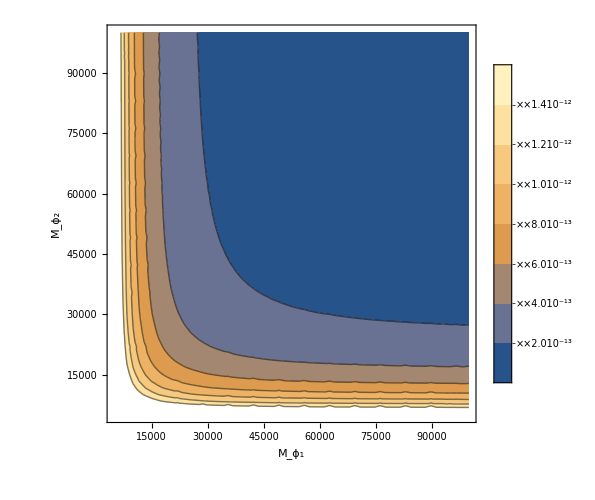

```mathematica
ContourPlot[Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,{{Mϕ1,0},{0,Mϕ2}}^2,lambda6Input]⟦2,2⟧],{Mϕ1,5 10^3,10^5},{Mϕ2,5 10^3,10^5},
FrameLabel->{"M_ϕ_1","M_ϕ_2"},
ImageSize->500,
PlotLegends->Automatic]
```

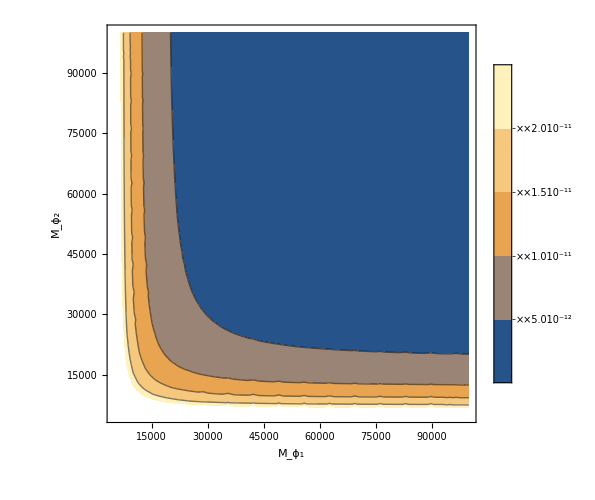

```mathematica
ContourPlot[Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,{{Mϕ1,0},{0,Mϕ2}}^2,lambda6Input]⟦3,3⟧],{Mϕ1,5 10^3,10^5},{Mϕ2,5 10^3,10^5},
FrameLabel->{"M_ϕ_1","M_ϕ_2"},
ImageSize->500,
PlotLegends->Automatic]
```

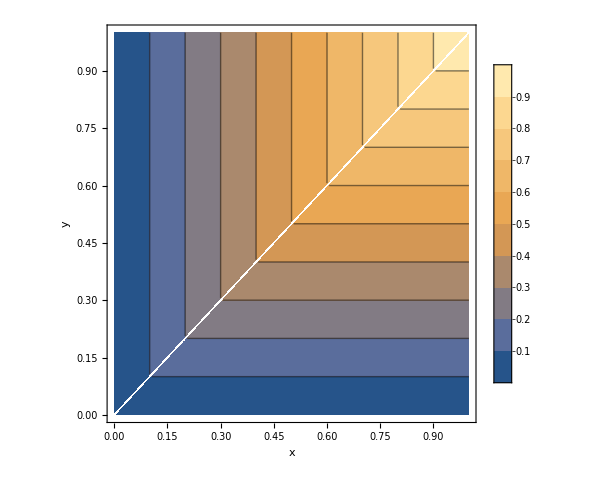

```mathematica
ContourPlot[Min[x,y],{x,0,1},{y,0,1},
FrameLabel->{"x","y"},
ImageSize->500,
PlotLegends->Automatic]
```

## LogPlot

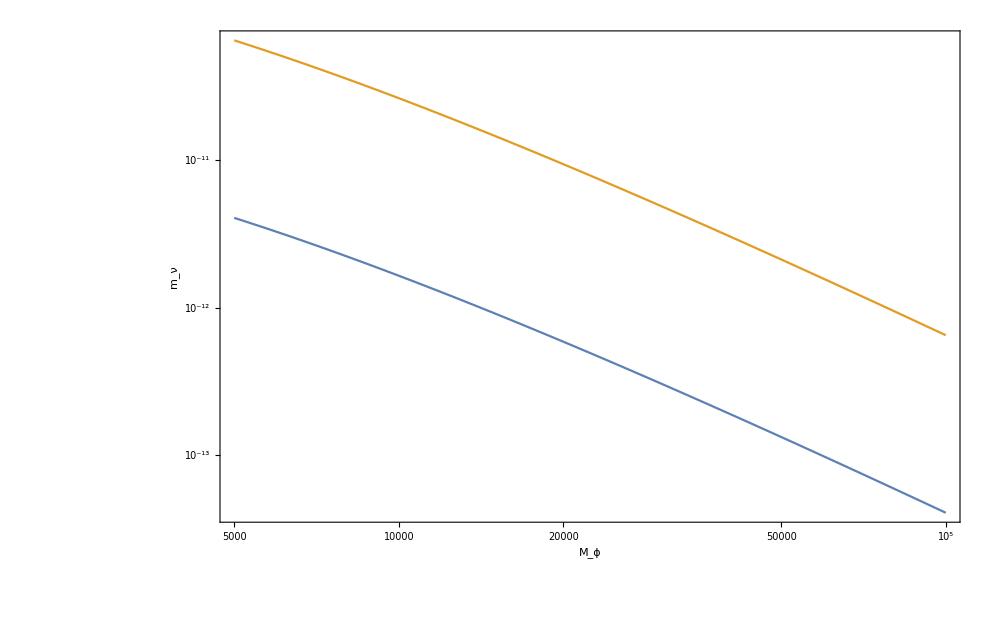

```mathematica
LogLogPlot[{Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,{{Mϕ,0},{0,Mϕ}}^2,lambda6Input]⟦2,2⟧],Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,{{Mϕ,0},{0,Mϕ}}^2,lambda6Input]⟦3,3⟧]},{Mϕ,5 10^3,10^5},
FrameLabel->{"M_ϕ","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

Vary fermion masses

## Fixed parameters

```mathematica
lambda4Input=5 10^-3;
lambda5Input =5 10^-3;
```

```mathematica
mCPsiInput=10^3;
mpsipsipInput=10^3;
```

```mathematica
MPHI2 = {{5 10^4,0},{0,5 10^4}}^2;
```

```mathematica
lambda6Input={{5 10^-3,5 10^-3},{5 10^-3,5 10^-3},{5 10^-3,5 10^-3}};
```

## Contour

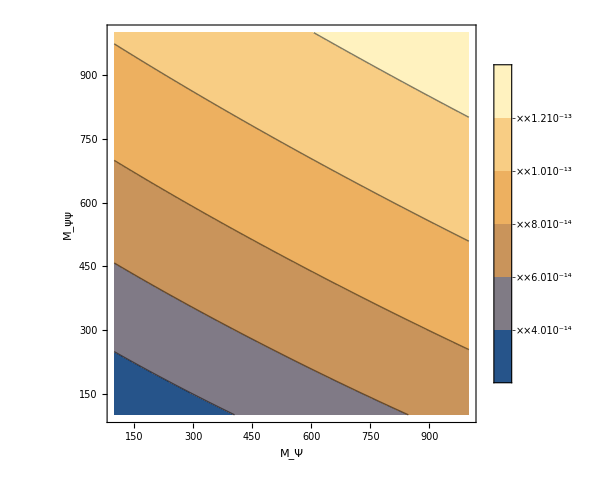

```mathematica
ContourPlot[Abs[Dnuoutput[lambda4Input,lambda5Input,Subscript[M, Ψ],Subscript[M, ψψ],MPHI2,lambda6Input]⟦2,2⟧],{Subscript[M, Ψ],10^2,10^3},{Subscript[M, ψψ],10^2,10^3},
FrameLabel->{"M_Ψ","M_ψψ"},
ImageSize->500,
PlotLegends->Automatic]
```

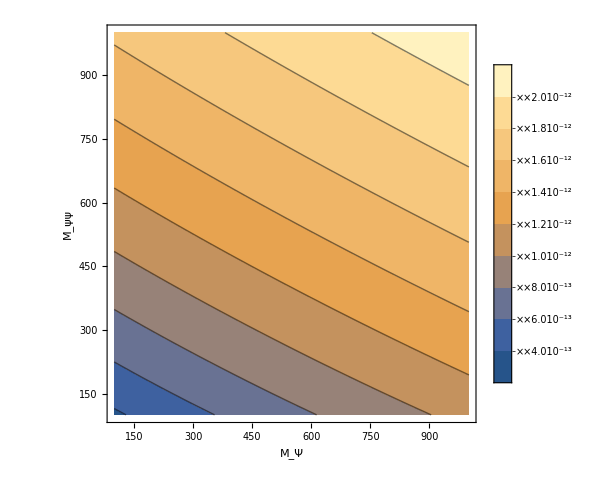

```mathematica
ContourPlot[Abs[Dnuoutput[lambda4Input,lambda5Input,Subscript[M, Ψ],Subscript[M, ψψ],MPHI2,lambda6Input]⟦3,3⟧],{Subscript[M, Ψ],10^2,10^3},{Subscript[M, ψψ],10^2,10^3},
FrameLabel->{"M_Ψ","M_ψψ"},
ImageSize->500,
PlotLegends->Automatic]
```

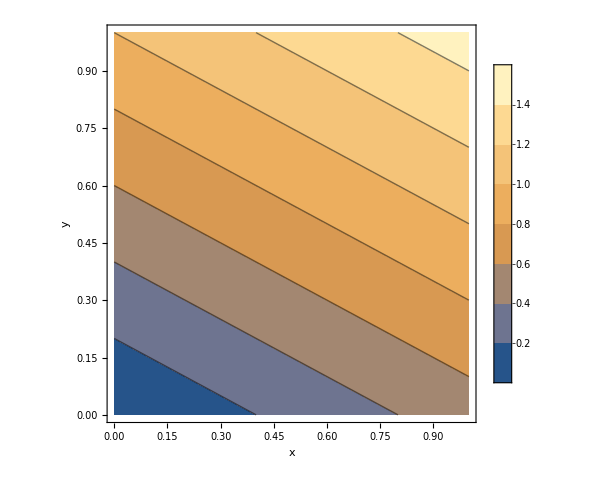

```mathematica
ContourPlot[0.5x+y,{x,0,1},{y,0,1},
FrameLabel->{"x","y"},
ImageSize->500,
PlotLegends->Automatic]
```

## LogPlot

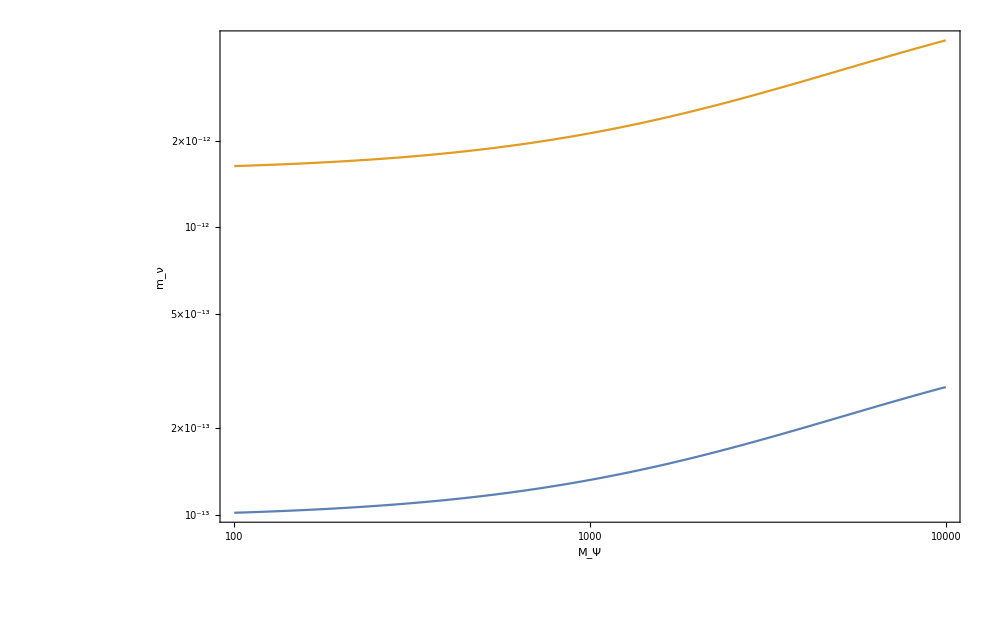

```mathematica
LogLogPlot[{Abs[Dnuoutput[lambda4Input,lambda5Input,MCPsi,mpsipsipInput,MPHI2,lambda6Input]⟦2,2⟧],Abs[Dnuoutput[lambda4Input,lambda5Input,MCPsi,mpsipsipInput,MPHI2,lambda6Input]⟦3,3⟧]},{MCPsi,10^2,10^4},
FrameLabel->{"M_Ψ","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

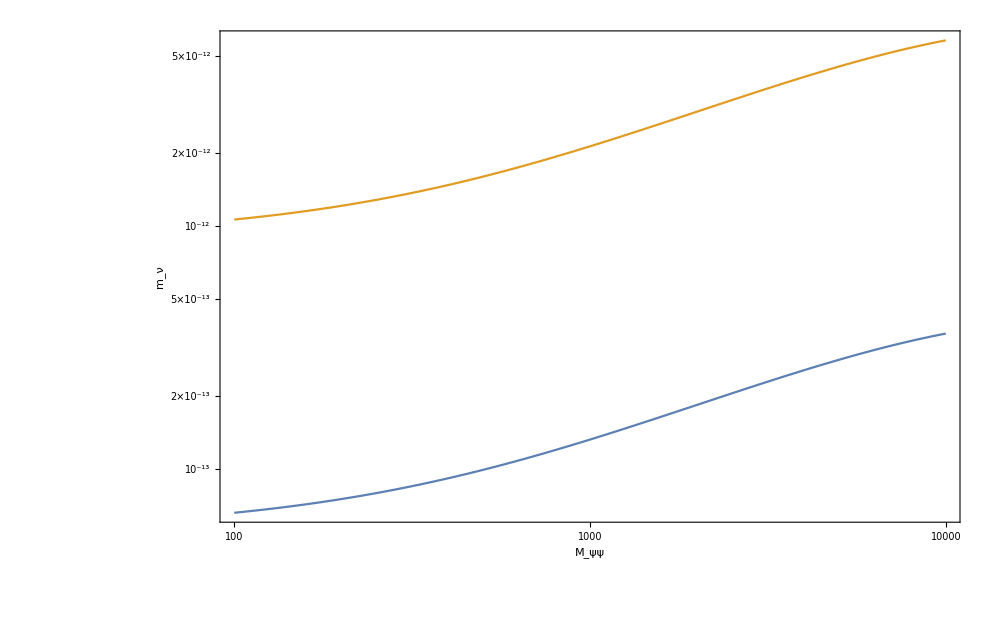

```mathematica
LogLogPlot[{Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsip,MPHI2,lambda6Input]⟦2,2⟧],Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsip,MPHI2,lambda6Input]⟦3,3⟧]},{mpsipsip,10^2,10^4},
FrameLabel->{"M_ψψ","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

Vary λ_6

## Fixed parameters

```mathematica
lambda4Input=5 10^-3;
lambda5Input =5 10^-3;
```

```mathematica
mCPsiInput=10^3;
mpsipsipInput=10^3;
```

```mathematica
MPHI2 = {{5 10^4,0},{0,5 10^4}}^2;
```

```mathematica
lambda6Input={{5 10^-3,5 10^-3},{5 10^-3,5 10^-3},{5 10^-3,5 10^-3}};
```

## Contour

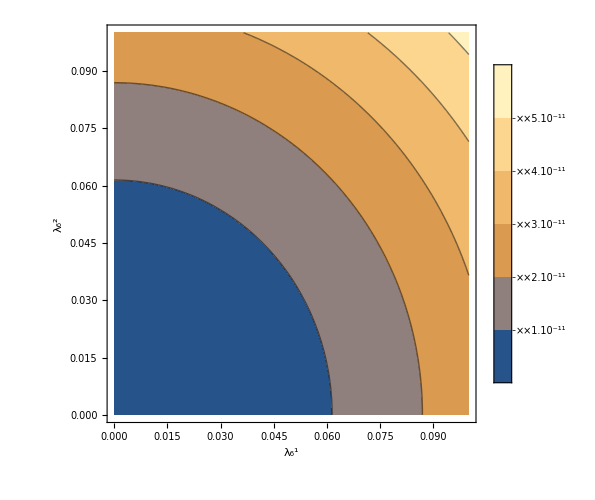

```mathematica
ContourPlot[Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,{{λ61,λ62},{λ61,λ62},{λ61,λ62}}]⟦2,2⟧],{λ61,10^-5,10^-1},{λ62,10^-5,10^-1},
FrameLabel->{"λ_6^1","λ_6^2"},
ImageSize->500,
PlotLegends->Automatic]
```

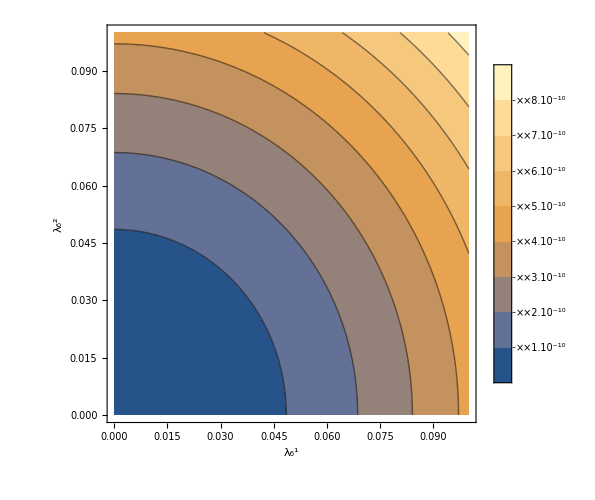

```mathematica
ContourPlot[Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,{{λ61,λ62},{λ61,λ62},{λ61,λ62}}]⟦3,3⟧],{λ61,10^-5,10^-1},{λ62,10^-5,10^-1},
FrameLabel->{"λ_6^1","λ_6^2"},
ImageSize->500,
PlotLegends->Automatic]
```

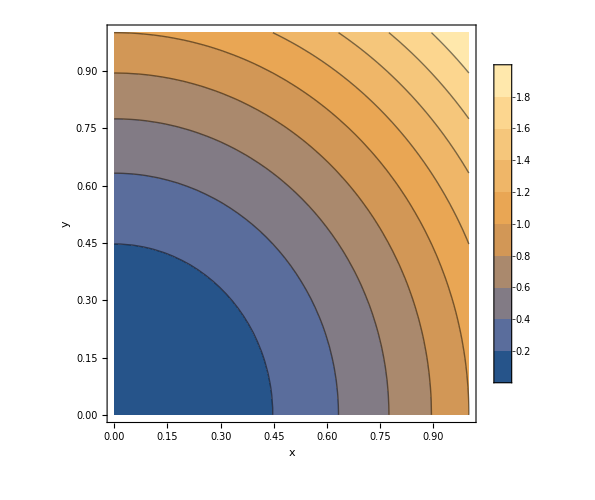

```mathematica
ContourPlot[x^2+y^2,{x,0,1},{y,0,1},
FrameLabel->{"x","y"},
ImageSize->500,
PlotLegends->Automatic]
```

## LogPlot

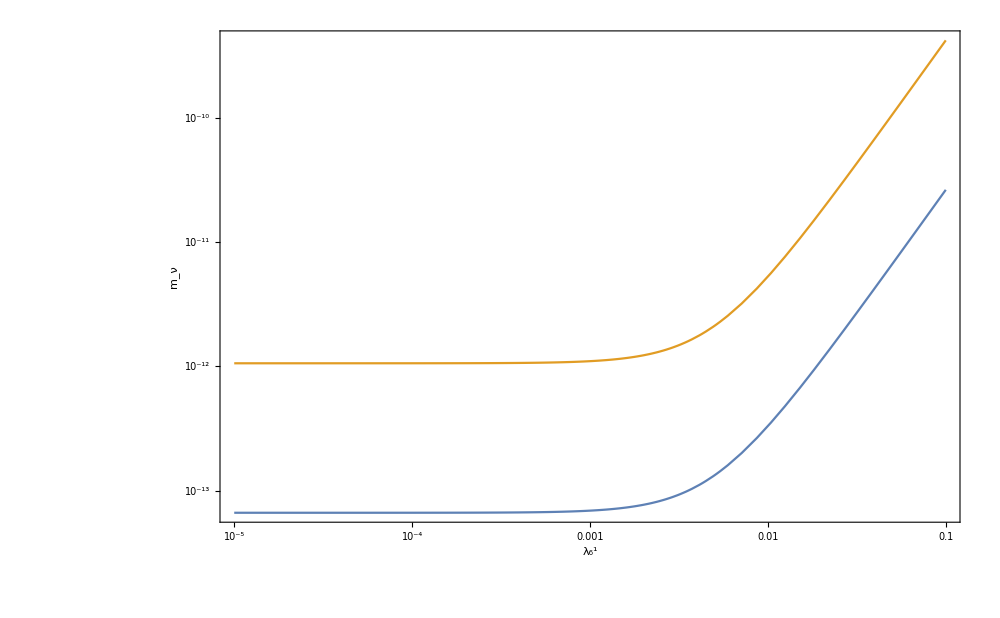

```mathematica
LogLogPlot[{Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,{{λ61,lambda6Input⟦1,2⟧},{λ61,lambda6Input⟦2,2⟧},{λ61,lambda6Input⟦3,2⟧}}]⟦2,2⟧],Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,{{λ61,lambda6Input⟦1,2⟧},{λ61,lambda6Input⟦2,2⟧},{λ61,lambda6Input⟦3,2⟧}}]⟦3,3⟧]},{λ61,10^-5,10^-1},
FrameLabel->{"λ_6^1","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

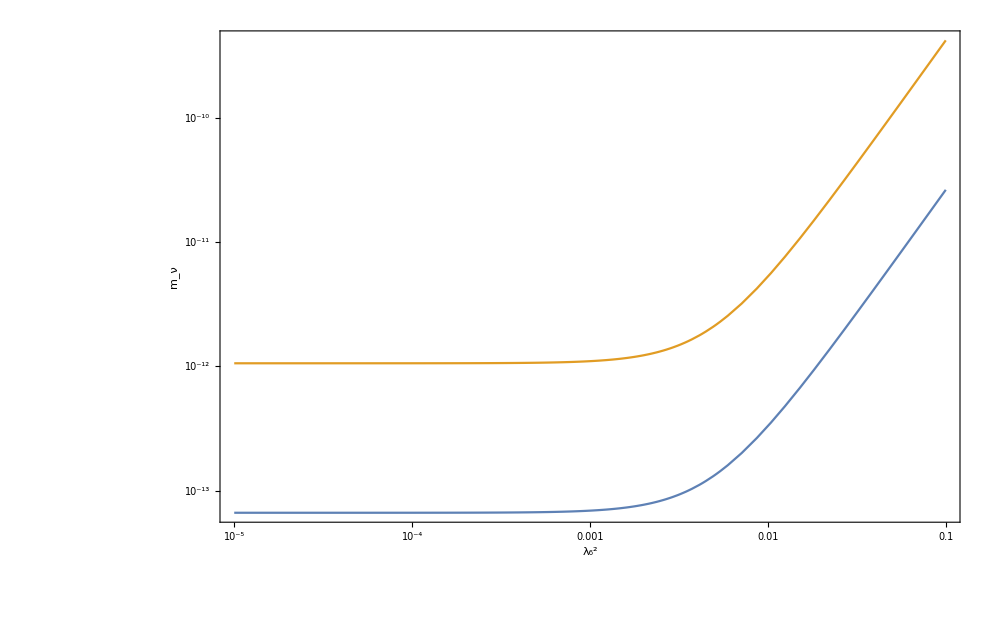

```mathematica
LogLogPlot[{Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,{{lambda6Input⟦1,1⟧,λ62},{lambda6Input⟦2,1⟧,λ62},{lambda6Input⟦3,1⟧,λ62}}]⟦2,2⟧],Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,{{lambda6Input⟦1,1⟧,λ62},{lambda6Input⟦2,1⟧,λ62},{lambda6Input⟦3,1⟧,λ62}}]⟦3,3⟧]},{λ62,10^-5,10^-1},
FrameLabel->{"λ_6^2","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

Vary λ_4 & λ_5

## Fixed parameters

```mathematica
lambda4Input=5 10^-3;
lambda5Input =5 10^-3;
```

```mathematica
mCPsiInput=10^3;
mpsipsipInput=10^3;
```

```mathematica
MPHI2 = {{5 10^4,0},{0,5 10^4}}^2;
```

```mathematica
lambda6Input={{5 10^-3,5 10^-3},{5 10^-3,5 10^-3},{5 10^-3,5 10^-3}};
```

## Contour

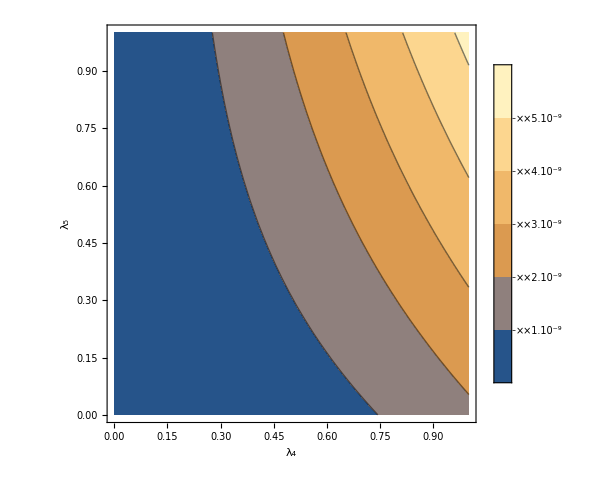

```mathematica
ContourPlot[Abs[Dnuoutput[λ4,λ5,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦2,2⟧],{λ4,10^-5,1},{λ5,10^-5,1},
FrameLabel->{"λ_4","λ_5"},
ImageSize->500,
PlotLegends->Automatic]
```

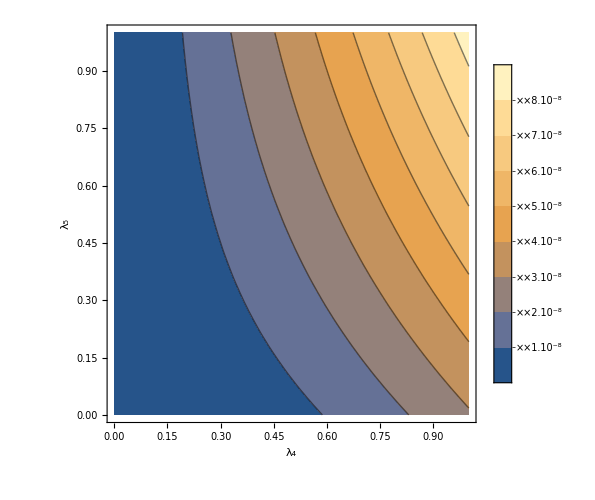

```mathematica
ContourPlot[Abs[Dnuoutput[λ4,λ5,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦3,3⟧],{λ4,10^-5,1},{λ5,10^-5,1},
FrameLabel->{"λ_4","λ_5"},
ImageSize->500,
PlotLegends->Automatic]
```

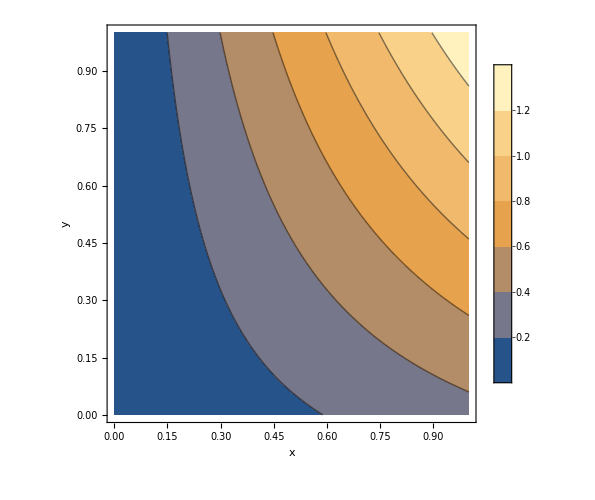

```mathematica
ContourPlot[x (y+0.34),{x,0,1},{y,0,1},
FrameLabel->{"x","y"},
ImageSize->500,
PlotLegends->Automatic]
```

## LogPlot

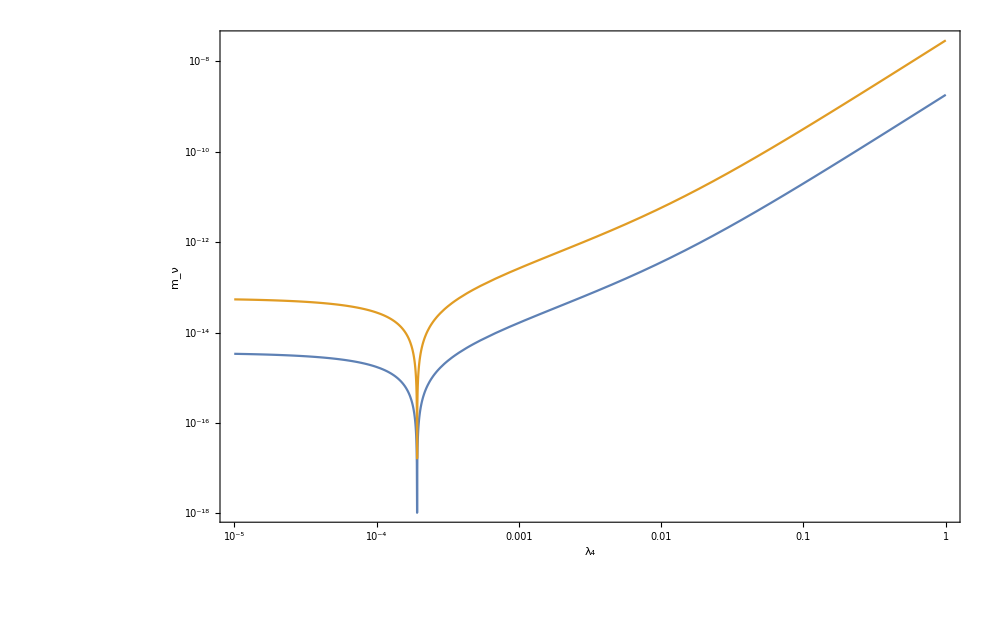

```mathematica
LogLogPlot[{Abs[Dnuoutput[λ4,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦2,2⟧],Abs[Dnuoutput[λ4,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦3,3⟧]},{λ4,10^-5,1},
FrameLabel->{"λ_4","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

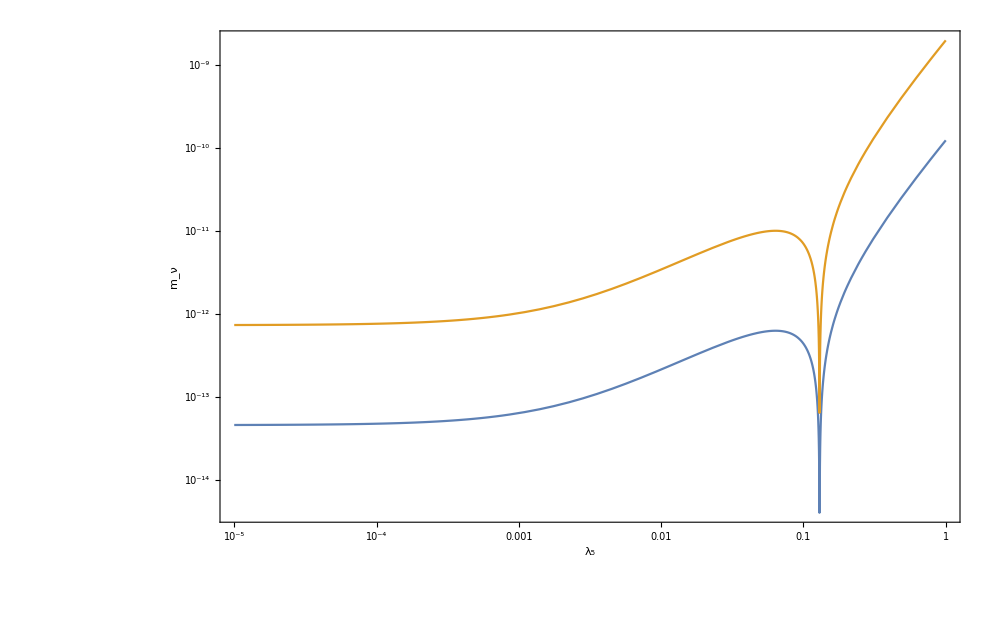

```mathematica
LogLogPlot[{Abs[Dnuoutput[lambda4Input,λ5,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦2,2⟧],Abs[Dnuoutput[lambda4Input,λ5,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦3,3⟧]},{λ5,10^-5,1},
FrameLabel->{"λ_5","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

Outcomes

Neutrino masses have a mild dependence on the Scalar Masses.
The neutrino masses decrease linearly with the scalar masses.
Neutrino masses set by the lightest scalar.

Neutrino masses have a small dependence  on the fermion masses.
They grow with the fermion masses.
Neutrino masses set by (k M_Ψ + M_ψψ') [k~0.5]

Neutrino masses have a strong dependence on the λ_6 coupling.
The masses of the neutrinos scale linearly with the coupling to the scalar that is stronger.
Neutrino masses set by ((λ_6^1)^2 + (λ_6^2)^2)

Neutrino masses have a strong dependence on the  λ_4 and λ_5 coupling.
They grow grow exponentially with the couplings except for a region with a dip.
The position of the dip depends on other parameters. It appears for small λ_4 and for large λ_5.
Neutrino masses set by (λ_4(λ_5+k)) [k~0.34]

## Scalar Dark Matter

We want to work in the scenario of Triplet Scalar Dark Matter.
This means that the new scalar masses have to be smaller than the new fermion masses.

Vary scalar masses

## Fixed parameters

```mathematica
lambda4Input=5 10^-3;
lambda5Input =5 10^-3;
```

```mathematica
mCPsiInput=10^4;
mpsipsipInput=10^4;
```

```mathematica
MPHI2 = {{10^3,0},{0,10^3}}^2;
```

```mathematica
lambda6Input={{5 10^-3,5 10^-3},{5 10^-3,5 10^-3},{5 10^-3,5 10^-3}};
```

## Contour

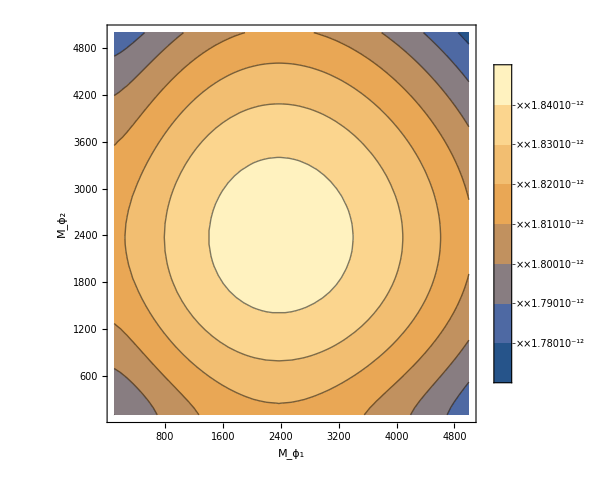

```mathematica
ContourPlot[Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,{{Mϕ1,0},{0,Mϕ2}}^2,lambda6Input]⟦2,2⟧],{Mϕ1,10^2,5 10^3},{Mϕ2,10^2,5 10^3},
FrameLabel->{"M_ϕ_1","M_ϕ_2"},
ImageSize->500,
PlotLegends->Automatic]
```

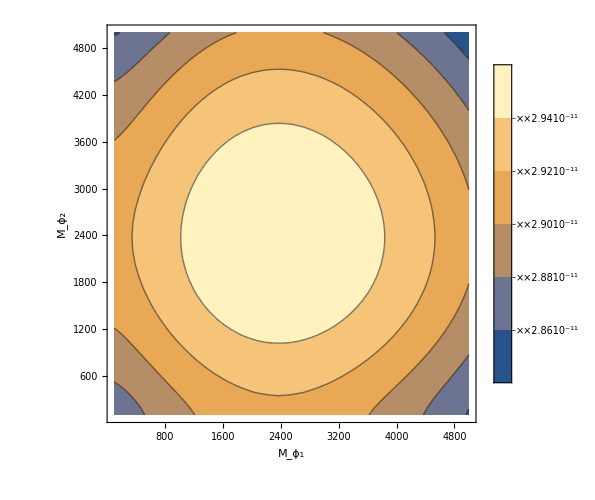

```mathematica
ContourPlot[Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,{{Mϕ1,0},{0,Mϕ2}}^2,lambda6Input]⟦3,3⟧],{Mϕ1,10^2,5 10^3},{Mϕ2,10^2,5 10^3},
FrameLabel->{"M_ϕ_1","M_ϕ_2"},
ImageSize->500,
PlotLegends->Automatic]
```

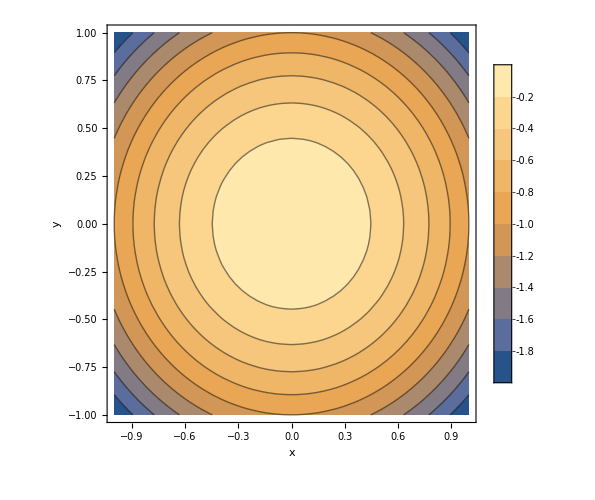

```mathematica
ContourPlot[-(x^2+y^2),{x,-1,1},{y,-1,1},
FrameLabel->{"x","y"},
ImageSize->500,
PlotLegends->Automatic]
```

## LogPlot

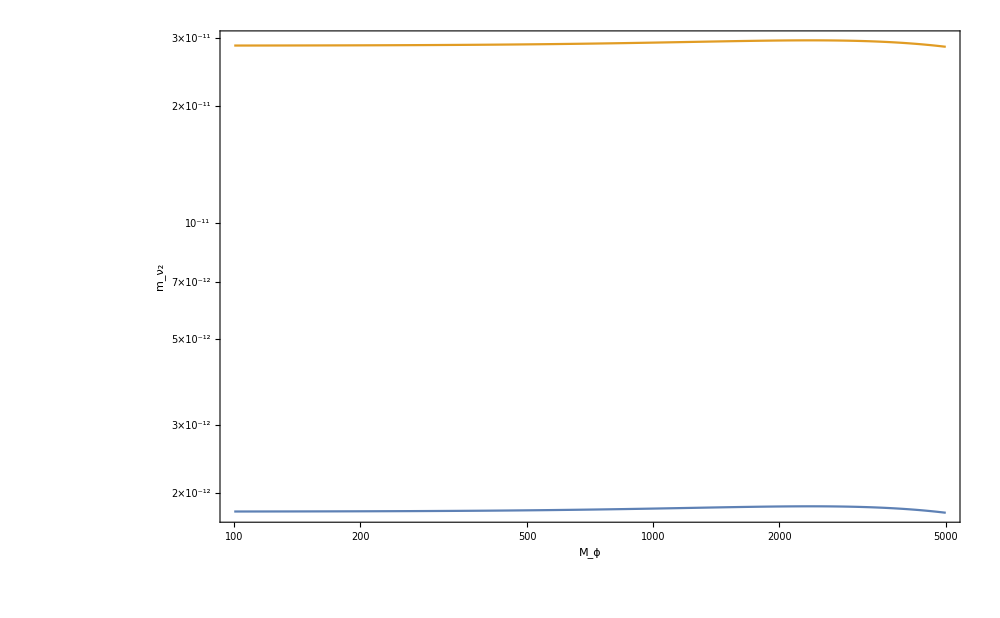

```mathematica
LogLogPlot[{Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,{{Mϕ,0},{0,Mϕ}}^2,lambda6Input]⟦2,2⟧],Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,{{Mϕ,0},{0,Mϕ}}^2,lambda6Input]⟦3,3⟧]},{Mϕ,10^2,5 10^3},
FrameLabel->{"M_ϕ","m_ν_2"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

Vary fermion masses

## Fixed parameters

```mathematica
lambda4Input=5 10^-3;
lambda5Input =5 10^-3;
```

```mathematica
mCPsiInput=10^4;
mpsipsipInput=10^4;
```

```mathematica
MPHI2 = {{10^3,0},{0,10^3}}^2;
```

```mathematica
lambda6Input={{5 10^-3,5 10^-3},{5 10^-3,5 10^-3},{5 10^-3,5 10^-3}};
```

## Contour

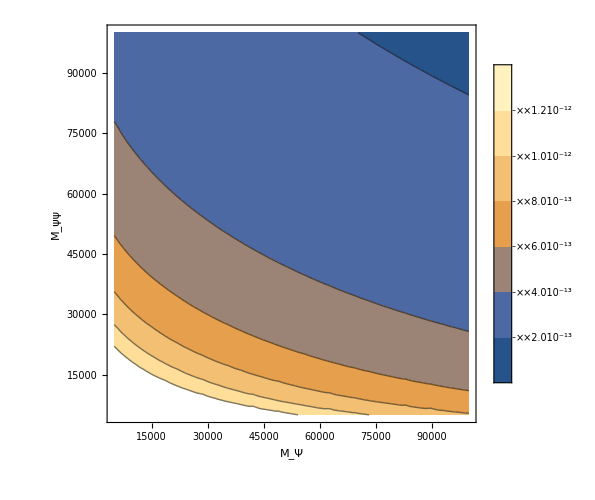

```mathematica
ContourPlot[Abs[Dnuoutput[lambda4Input,lambda5Input,Subscript[M, Ψ],Subscript[M, ψψ],MPHI2,lambda6Input]⟦2,2⟧],{Subscript[M, Ψ],5 10^3,10^5},{Subscript[M, ψψ],5 10^3,10^5},
FrameLabel->{"M_Ψ","M_ψψ"},
ImageSize->500,
PlotLegends->Automatic]
```

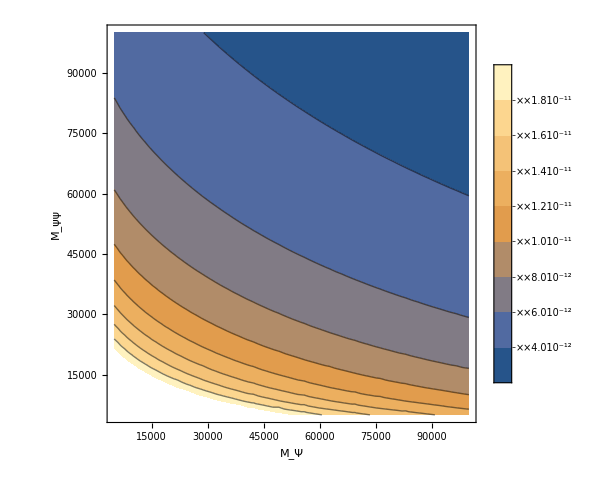

```mathematica
ContourPlot[Abs[Dnuoutput[lambda4Input,lambda5Input,Subscript[M, Ψ],Subscript[M, ψψ],MPHI2,lambda6Input]⟦3,3⟧],{Subscript[M, Ψ],5 10^3,10^5},{Subscript[M, ψψ],5 10^3,10^5},
FrameLabel->{"M_Ψ","M_ψψ"},
ImageSize->500,
PlotLegends->Automatic]
```

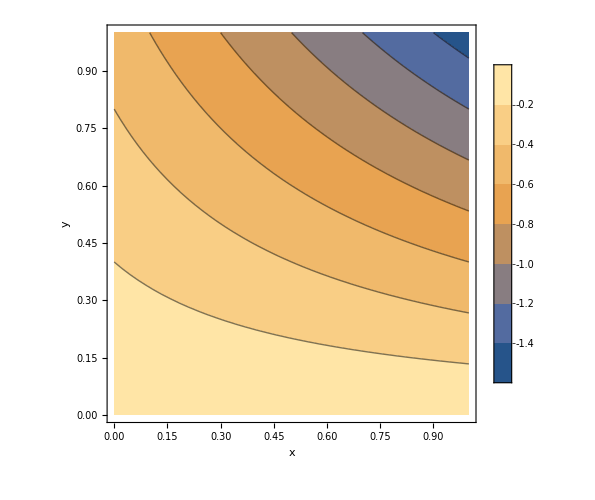

```mathematica
ContourPlot[-(x+0.5) y,{x,0,1},{y,0,1},
FrameLabel->{"x","y"},
ImageSize->500,
PlotLegends->Automatic]
```

## LogPlot

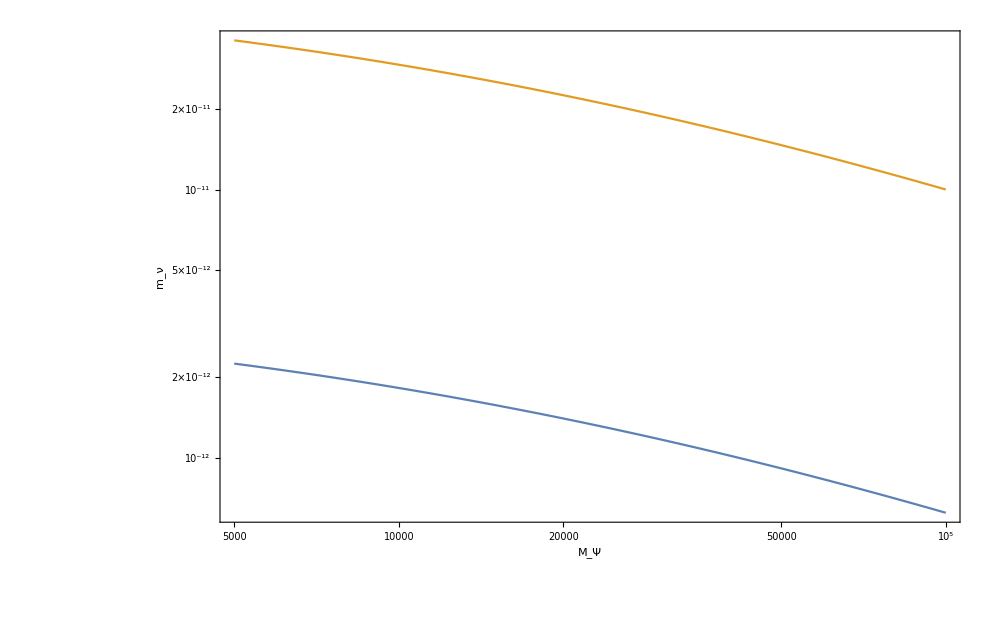

```mathematica
LogLogPlot[{Abs[Dnuoutput[lambda4Input,lambda5Input,MCPsi,mpsipsipInput,MPHI2,lambda6Input]⟦2,2⟧],Abs[Dnuoutput[lambda4Input,lambda5Input,MCPsi,mpsipsipInput,MPHI2,lambda6Input]⟦3,3⟧]},{MCPsi,5 10^3,10^5},
FrameLabel->{"M_Ψ","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

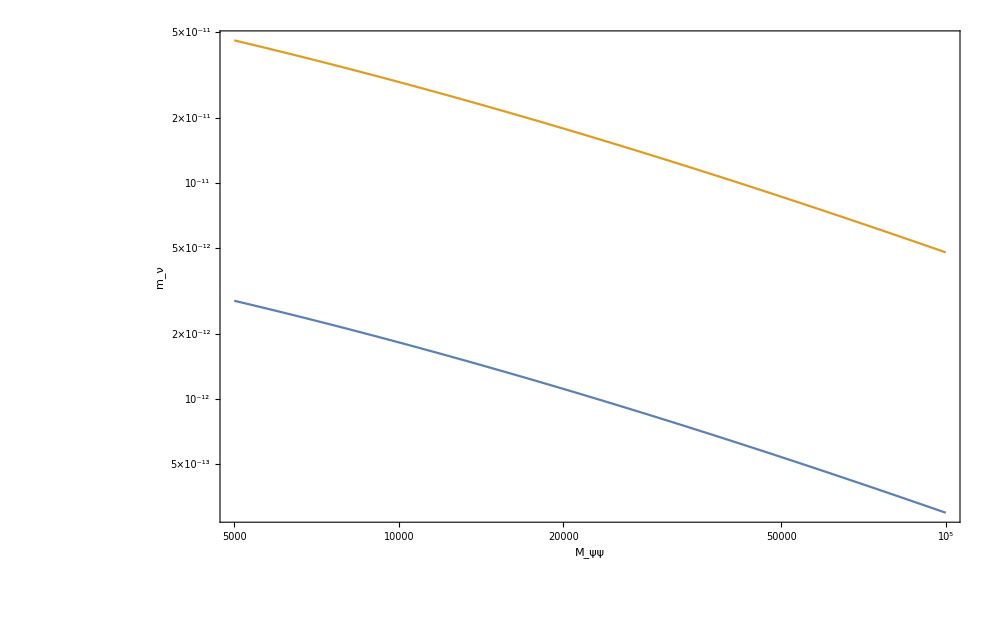

```mathematica
LogLogPlot[{Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsip,MPHI2,lambda6Input]⟦2,2⟧],Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsip,MPHI2,lambda6Input]⟦3,3⟧]},{mpsipsip,5 10^3,10^5},
FrameLabel->{"M_ψψ","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

Vary λ_6

## Fixed parameters

```mathematica
lambda4Input=5 10^-3;
lambda5Input =5 10^-3;
```

```mathematica
mCPsiInput=10^4;
mpsipsipInput=10^4;
```

```mathematica
MPHI2 = {{10^3,0},{0,10^3}}^2;
```

```mathematica
lambda6Input={{5 10^-3,5 10^-3},{5 10^-3,5 10^-3},{5 10^-3,5 10^-3}};
```

## Contour

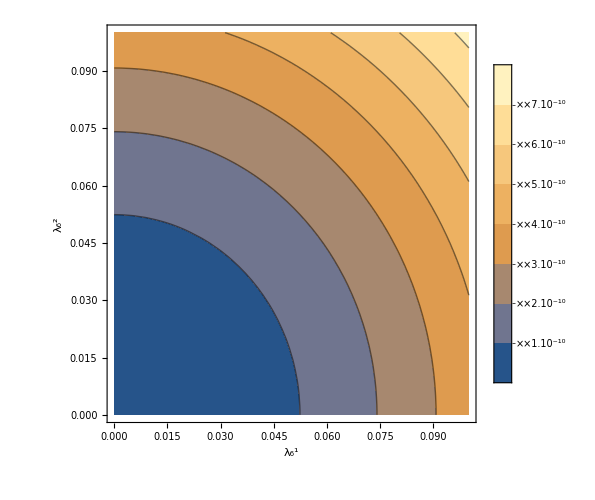

```mathematica
ContourPlot[Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,{{λ61,λ62},{λ61,λ62},{λ61,λ62}}]⟦2,2⟧],{λ61,10^-5,10^-1},{λ62,10^-5,10^-1},
FrameLabel->{"λ_6^1","λ_6^2"},
ImageSize->500,
PlotLegends->Automatic]
```

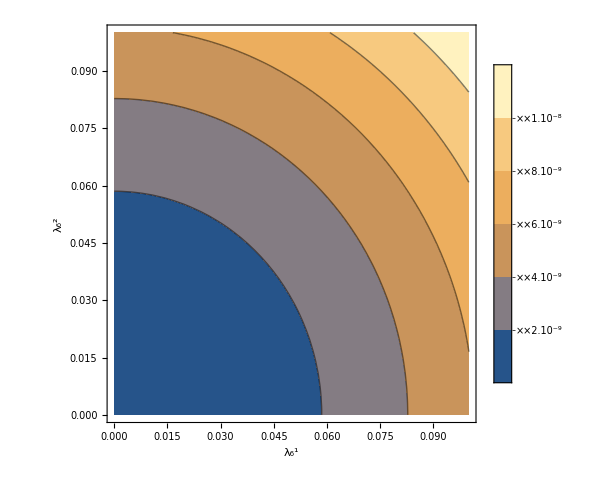

```mathematica
ContourPlot[Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,{{λ61,λ62},{λ61,λ62},{λ61,λ62}}]⟦3,3⟧],{λ61,10^-5,10^-1},{λ62,10^-5,10^-1},
FrameLabel->{"λ_6^1","λ_6^2"},
ImageSize->500,
PlotLegends->Automatic]
```

```mathematica
ContourPlot[x^2+y^2,{x,0,1},{y,0,1},
FrameLabel->{"x","y"},
ImageSize->500,
PlotLegends->Automatic]
```

-Graphics-

## LogPlot

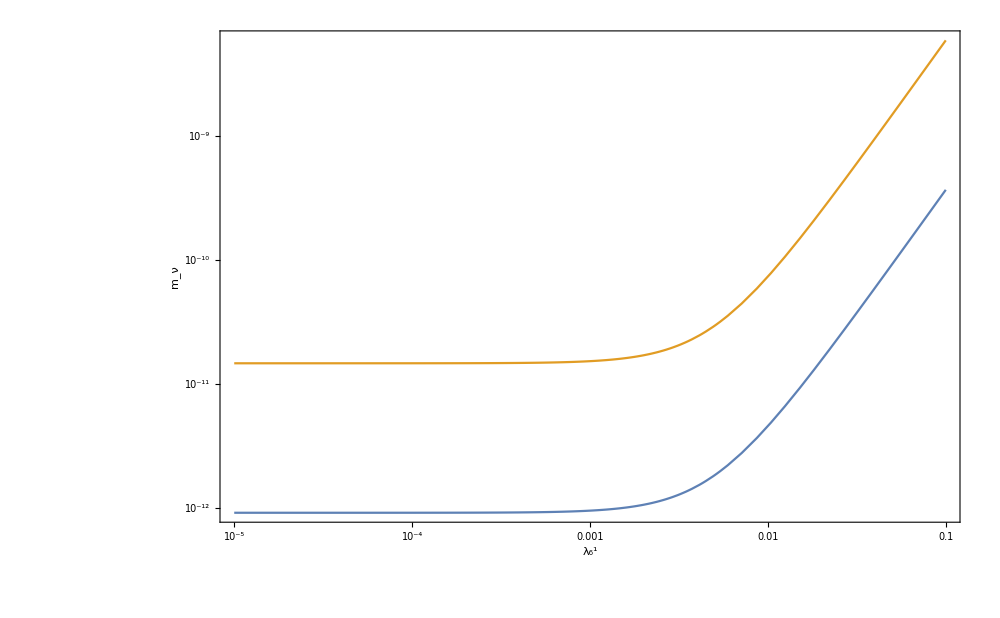

```mathematica
LogLogPlot[{Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,{{λ61,lambda6Input⟦1,2⟧},{λ61,lambda6Input⟦2,2⟧},{λ61,lambda6Input⟦3,2⟧}}]⟦2,2⟧],Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,{{λ61,lambda6Input⟦1,2⟧},{λ61,lambda6Input⟦2,2⟧},{λ61,lambda6Input⟦3,2⟧}}]⟦3,3⟧]},{λ61,10^-5,10^-1},
FrameLabel->{"λ_6^1","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

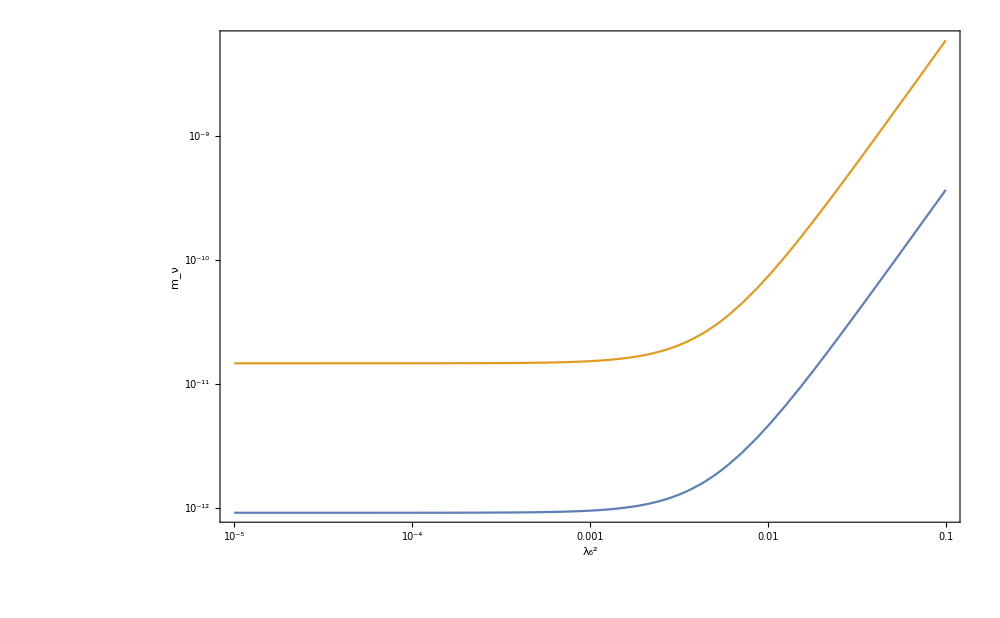

```mathematica
LogLogPlot[{Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,{{lambda6Input⟦1,1⟧,λ62},{lambda6Input⟦2,1⟧,λ62},{lambda6Input⟦3,1⟧,λ62}}]⟦2,2⟧],Abs[Dnuoutput[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,{{lambda6Input⟦1,1⟧,λ62},{lambda6Input⟦2,1⟧,λ62},{lambda6Input⟦3,1⟧,λ62}}]⟦3,3⟧]},{λ62,10^-5,10^-1},
FrameLabel->{"λ_6^2","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

Vary λ_4 & λ_5

## Fixed parameters

```mathematica
lambda4Input=5 10^-3;
lambda5Input =5 10^-3;
```

```mathematica
mCPsiInput=10^4;
mpsipsipInput=10^4;
```

```mathematica
MPHI2 = {{10^3,0},{0,10^3}}^2;
```

```mathematica
lambda6Input={{5 10^-3,5 10^-3},{5 10^-3,5 10^-3},{5 10^-3,5 10^-3}};
```

## Contour

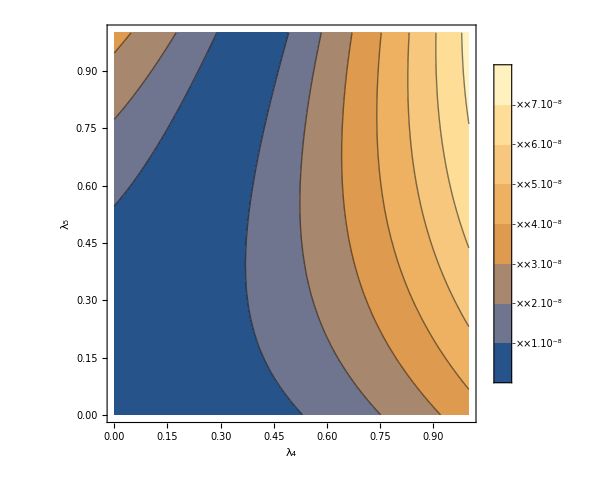

```mathematica
ContourPlot[Abs[Dnuoutput[λ4,λ5,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦2,2⟧],{λ4,10^-5,1},{λ5,10^-5,1},
FrameLabel->{"λ_4","λ_5"},
ImageSize->500,
PlotLegends->Automatic]
```

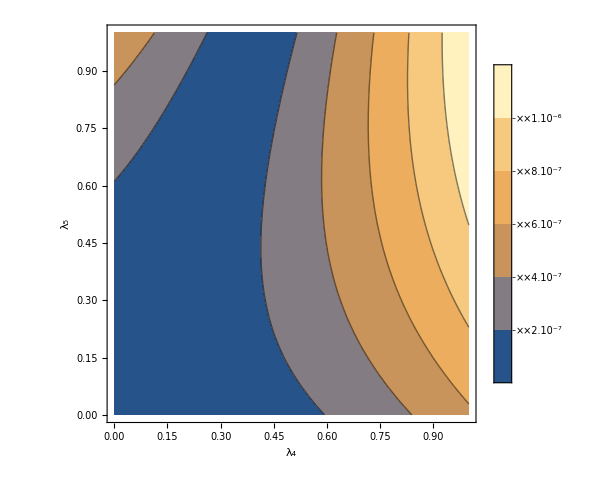

```mathematica
ContourPlot[Abs[Dnuoutput[λ4,λ5,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦3,3⟧],{λ4,10^-5,1},{λ5,10^-5,1},
FrameLabel->{"λ_4","λ_5"},
ImageSize->500,
PlotLegends->Automatic]
```

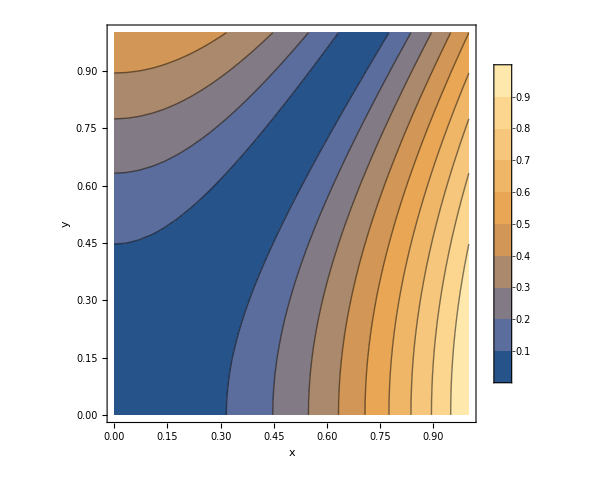

```mathematica
ContourPlot[Abs[x^2-0.5 y^2],{x,0,1},{y,0,1},
FrameLabel->{"x","y"},
ImageSize->500,
PlotLegends->Automatic]
```

## LogPlot

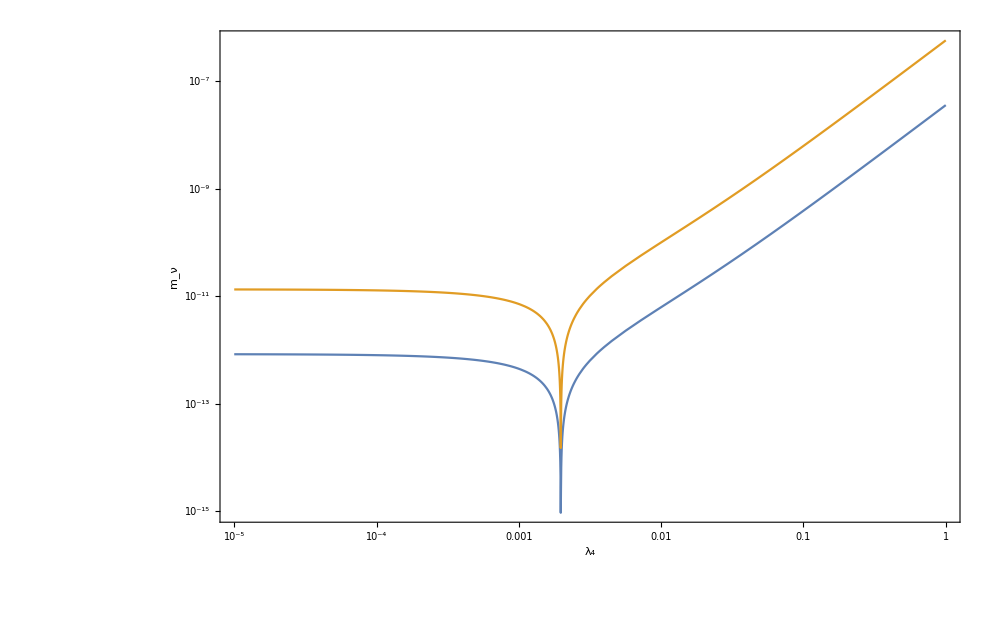

```mathematica
LogLogPlot[{Abs[Dnuoutput[λ4,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦2,2⟧],Abs[Dnuoutput[λ4,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦3,3⟧]},{λ4,10^-5,1},
FrameLabel->{"λ_4","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

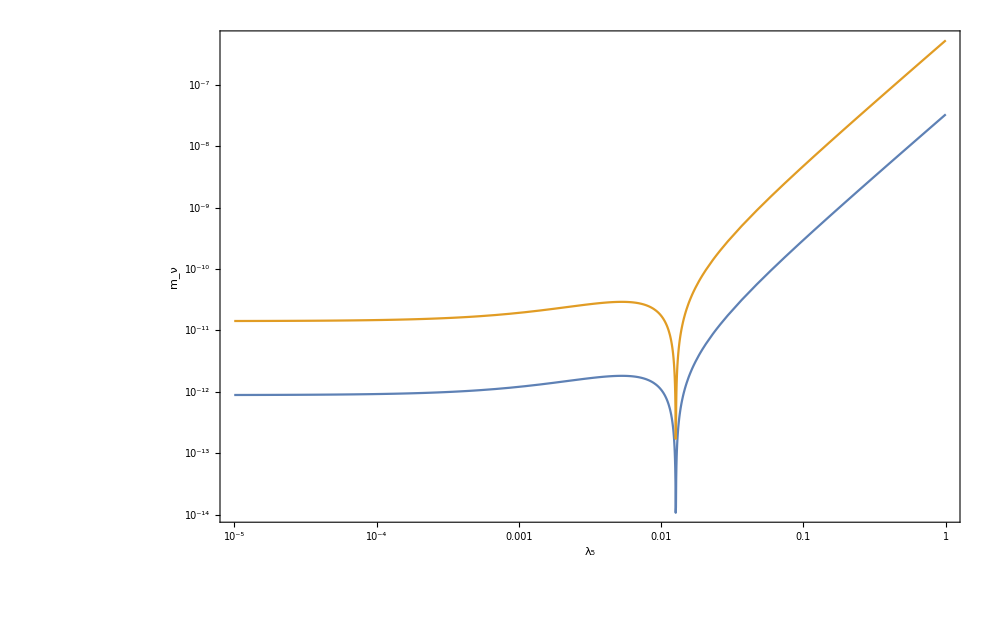

```mathematica
LogLogPlot[{Abs[Dnuoutput[lambda4Input,λ5,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦2,2⟧],Abs[Dnuoutput[lambda4Input,λ5,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦3,3⟧]},{λ5,10^-5,1},
FrameLabel->{"λ_5","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

Vary λ_4 & λ_5 test

## Fixed parameters

```mathematica
lambda4Input=5 10^-3;
lambda5Input =5 10^-3;
```

```mathematica
mCPsiInput=3.33 10^3;
mpsipsipInput=1.66 10^3;
```

```mathematica
MPHI2 = {{10^3,0},{0,3.33 10^3}}^2;
```

```mathematica
lambda6Input={{10^-1,10^-5},{10^-1,10^-5},{10^-1,10^-5}};
```

## Contour

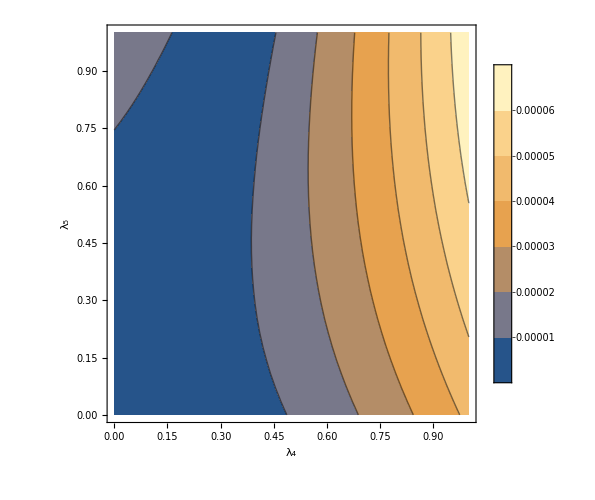

```mathematica
ContourPlot[Abs[Dnuoutput[λ4,λ5,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦2,2⟧],{λ4,10^-5,1},{λ5,10^-5,1},
FrameLabel->{"λ_4","λ_5"},
ImageSize->500,
PlotLegends->Automatic]
```

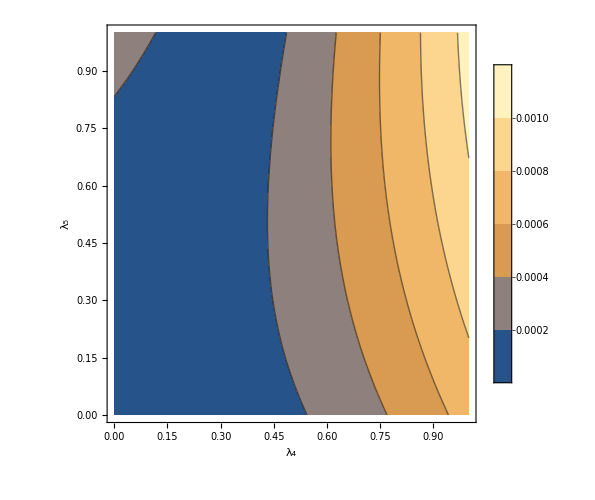

```mathematica
ContourPlot[Abs[Dnuoutput[λ4,λ5,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦3,3⟧],{λ4,10^-5,1},{λ5,10^-5,1},
FrameLabel->{"λ_4","λ_5"},
ImageSize->500,
PlotLegends->Automatic]
```

```mathematica
ContourPlot[Abs[x^2-0.5 y^2],{x,0,1},{y,0,1},
FrameLabel->{"x","y"},
ImageSize->500,
PlotLegends->Automatic]
```

-Graphics-

## LogPlot

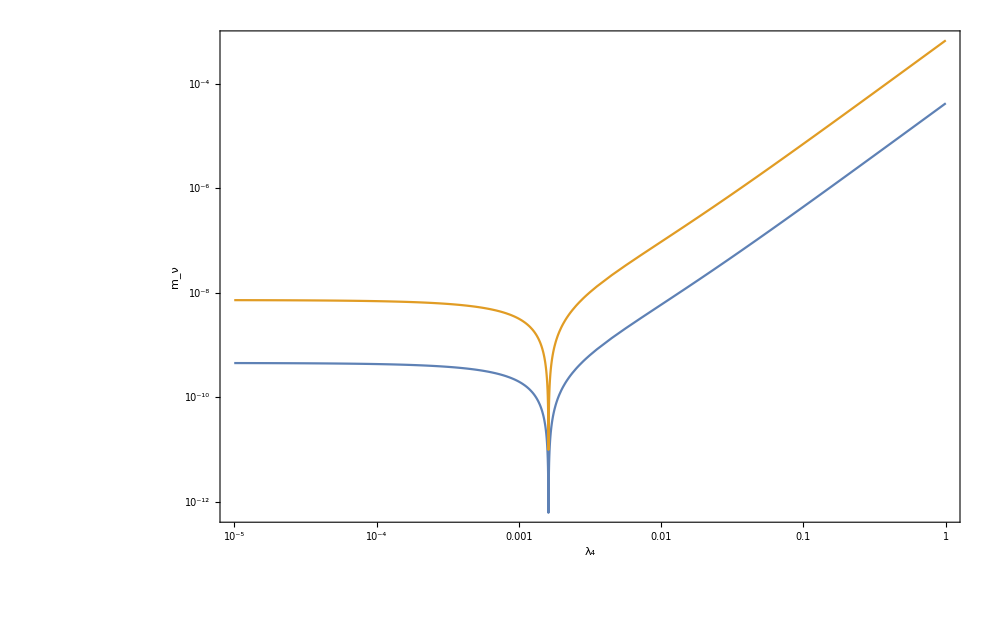

```mathematica
LogLogPlot[{Abs[Dnuoutput[λ4,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦2,2⟧],Abs[Dnuoutput[λ4,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦3,3⟧]},{λ4,10^-5,1},
FrameLabel->{"λ_4","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

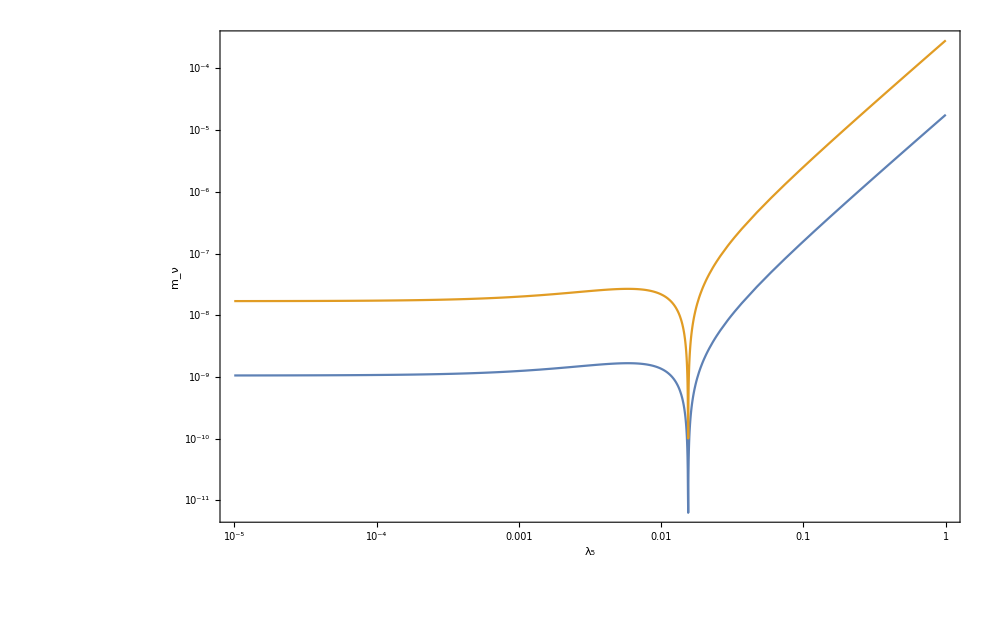

```mathematica
LogLogPlot[{Abs[Dnuoutput[lambda4Input,λ5,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦2,2⟧],Abs[Dnuoutput[lambda4Input,λ5,mCPsiInput,mpsipsipInput,MPHI2,lambda6Input]⟦3,3⟧]},{λ5,10^-5,1},
FrameLabel->{"λ_5","m_ν"},
ImageSize->1000,
LabelStyle->24,
Frame->True]
```

Outcomes

Neutrino masses have a null dependence on the Scalar Masses.
The neutrino masses follow (-(M_ϕ_1^2+M_ϕ_2^2))

Neutrino masses have a mild dependence on the Fermion Masses. Their mass decreases with the fermion masses.
The neutrino masses follow (-(M_Ψ+k)M_ψψ') [k~0.5]

Neutrino masses have a strong dependence on the λ_6 coupling. The masses of the neutrinos scale linearly with the coupling to the scalar that is stronger.
Neutrino masses set by ((λ_6^1)^2 + (λ_6^2)^2)

Neutrino masses have a strong dependence on the  λ_4 and λ_5 coupling.
They grow grow exponentially with the couplings except for a region with a dip.
The position of the dip depends on other parameters. It appears for small λ_4 and for large λ_5.
Neutrino masses set by |λ_4^2-k λ_5^2| [k~0.5]

## Outcomes Summary

The mass of the neutrinos have a strong dependence on the mass of the heaviest extra particle, both in the Fermionic and in the Scalar DM realization.
The mass of the lighter extra particle, which plays the role of the DM have very small effect on the neutrino masses.

In both cases neutrino masses have a strong dependence on the λ_6 coupling.
The masses of the neutrinos scale linearly with the coupling to the scalar that is stronger.

In both cases neutrino masses have a strong dependence on the couplings λ_4 and λ_5.
Neutrino masses grow exponentially with those couplings, except for the presence of a dip which position depends on the other parameters.
The dip in the λ_4 coupling tends to appear for small couplings, while the dip in the λ_5 coupling tends to appear for large couplings.
This is more true in the case of Fermionic DM, while the two dips are closer in the case of Scalar DM.

# Analytical Expansion

## Eigenvalues & Eigenvectors

```mathematica
C1=2 mCPsiInput^2+6 mpsipsipInput^2+3(lambda4Input^2+lambda5Input^2)v^2;
C2 = 4mCPsiInput(mCPsiInput^2-9 mpsipsipInput^2)+9((lambda4Input^2+lambda5Input^2)mCPsiInput+6lambda4Input lambda5Input mpsipsipInput)v^2;
```

```mathematica
B1=(-C2+√(C2^2-2 C1^3))^(1/3);
B2=C1/B1;
```

```mathematica
Λ1=1/3(mCPsiInput-(2)^(-2/3)B1-(2)^(-1/3)B2);
```

```mathematica
Λ2=1/3(mCPsiInput+(2)^(-2/3)(-1)^(1/3)B1+(2)^(-1/3)(-1)^(-1/3)B2);
```

```mathematica
Λ3=1/3(mCPsiInput+(2)^(-2/3)(-1)^(-1/3)B1+(2)^(-1/3)(-1)^(1/3)B2);
```

```mathematica
eigen[Λ_]:={√2 Abs[Λ^2-mpsipsipInput^2],v(mpsipsipInput lambda4Input+Λ lambda5Input),v(Λ lambda4Input+mpsipsipInput lambda5Input)}/√(2(Λ^2-mpsipsipInput^2)^2+v^2((Λ^2+mpsipsipInput^2)(lambda4Input^2+lambda5Input^2)+4mpsipsipInput Λ lambda4Input lambda5Input));
```

## Expansion

M_Ψ >> M_ψψ'

```mathematica
C1temp = C1/.lambda4Input->0/.lambda5Input->0/.v->0//N
```

2. mCPsiInput^2+6. mpsipsipInput^2

```mathematica
C2temp = C2/.lambda4Input->0/.lambda5Input->0/.v->0//Expand
```

4 mCPsiInput^3-36 mCPsiInput mpsipsipInput^2

```mathematica
B1temp=FullSimplify[Normal[Series[(-C2temp+√(C2temp^2-2 C1temp^3))^(1/3),{mpsipsipInput,0,1}]],mCPsiInput>0&&mpsipsipInput>0 ]
B2temp=Normal[Series[C1temp/B1temp,{mpsipsipInput,0,1}]]//FullSimplify
```

(0.793701+1.37473 ⅈ) mCPsiInput+(2.3811-1.37473 ⅈ) mpsipsipInput

(0.629961-1.09112 ⅈ) mCPsiInput+(1.88988+1.09112 ⅈ) mpsipsipInput

```mathematica
Λ1temp=1/3(mCPsiInput-(2)^(-2/3)B1temp-(2)^(-1/3)B2temp)//FullSimplify
```

(-1.44452×10^-16-2.956×10^-17 ⅈ) mCPsiInput-(1.-5.55112×10^-17 ⅈ) mpsipsipInput

```mathematica
Λ2temp=1/3(mCPsiInput+(2)^(-2/3)(-1)^(1/3)B1temp+(2)^(-1/3)(-1)^(-1/3)B2temp)//FullSimplify//N
```

(9.78258×10^-17+1.10319×10^-16 ⅈ) mCPsiInput+(1.+5.55112×10^-17 ⅈ) mpsipsipInput

```mathematica
Λ3temp=1/3(mCPsiInput+(2)^(-2/3)(-1)^(-1/3)B1temp+(2)^(-1/3)(-1)^(1/3)B2temp)//FullSimplify//N
```

1. mCPsiInput-(2.91619×10^-16+3.51344×10^-17 ⅈ) mpsipsipInput

```mathematica
(eigen[mpsipsipInput]⟦3⟧)^2//FullSimplify
```

1/2

```mathematica
(eigen[mCPsiInput]⟦3⟧)^2/.mpsipsipInput->0//FullSimplify
```

(lambda4Input^2 v^2)/(2 mCPsiInput^2+(lambda4Input^2+lambda5Input^2) v^2)

M_ψψ'>>M_Ψ

```mathematica
C1temp = Normal[Series[C1/.lambda4Input->0/.lambda5Input->0/.v->0,{mCPsiInput,0,1}]]
```

6 mpsipsipInput^2

```mathematica
C2temp = Normal[Series[C2/.lambda4Input->0/.lambda5Input->0/.v->0,{mCPsiInput,0,1}]]
```

-36 mCPsiInput mpsipsipInput^2

```mathematica
B1temp=FullSimplify[Normal[Series[(-C2temp+√(C2temp^2-2 C1temp^3))^(1/3),{mCPsiInput,0,1}]],mCPsiInput>0&&mpsipsipInput>0]
B2temp=Normal[Series[C1temp/B1temp,{mCPsiInput,0,1}]]
```

(-1)^(1/6) 2^(2/3) (-ⅈ mCPsiInput+√3 mpsipsipInput)

(-2)^(1/3) mCPsiInput-(-1)^(5/6) 2^(1/3) √3 mpsipsipInput

```mathematica
Λ1temp=1/3(mCPsiInput-(2)^(-2/3)B1temp-(2)^(-1/3)B2temp)//FullSimplify
```

-mpsipsipInput

```mathematica
Λ2temp=1/3(mCPsiInput+(2)^(-2/3)(-1)^(1/3)B1temp+(2)^(-1/3)(-1)^(-1/3)B2temp)//FullSimplify
```

mCPsiInput

```mathematica
Λ3temp=1/3(mCPsiInput+(2)^(-2/3)(-1)^(-1/3)B1temp+(2)^(-1/3)(-1)^(1/3)B2temp)//FullSimplify
```

mpsipsipInput

```mathematica
(eigen[Λ1temp]⟦3⟧)^2/.mCPsiInput->0//FullSimplify
```

1/2

```mathematica
(eigen[Λ2temp]⟦3⟧)^2//FullSimplify
```

((lambda4Input mCPsiInput+lambda5Input mpsipsipInput)^2 v^2)/(2 (mCPsiInput^2-mpsipsipInput^2)^2+(4 lambda4Input lambda5Input mCPsiInput mpsipsipInput+(lambda4Input^2+lambda5Input^2) (mCPsiInput^2+mpsipsipInput^2)) v^2)

```mathematica
(eigen[Λ3temp]⟦3⟧)^2/.mCPsiInput->0//FullSimplify
```

1/2

M_ψψ'=M_Ψ = M

```mathematica
C1temp = C1/.mCPsiInput->M/.mpsipsipInput->M/.lambda4Input->0/.lambda5Input->0/.v->0
```

8 M^2

```mathematica
C2temp = C2/.mCPsiInput->M/.mpsipsipInput->M/.lambda4Input->0/.lambda5Input->0/.v->0
```

-32 M^3

```mathematica
B1temp=Simplify[(-C2temp+√(C2temp^2-2 C1temp^3))^(1/3),M>0]
B2temp=C1temp/B1temp
```

2 2^(2/3) M

2 2^(1/3) M

```mathematica
Λ1temp=1/3(mCPsiInput-(2)^(-2/3)B1temp-(2)^(-1/3)B2temp)/.mCPsiInput->M
```

-M

```mathematica
Λ2temp=1/3(mCPsiInput+(2)^(-2/3)(-1)^(1/3)B1temp+(2)^(-1/3)(-1)^(-1/3)B2temp)/.mCPsiInput->M//FullSimplify
```

M

```mathematica
Λ3temp=1/3(mCPsiInput+(2)^(-2/3)(-1)^(-1/3)B1temp+(2)^(-1/3)(-1)^(1/3)B2temp)/.mCPsiInput->M//FullSimplify
```

M

Eigenvectors cannot be computed with normal procedure because of the degeneracy. Must compute them by hand.

```mathematica
(*(eigen[Λ1temp]⟦3⟧)^2/.mpsipsipInput->M//FullSimplify*)
```

```mathematica
(*(eigen[Λ2temp]⟦3⟧)^2/.mpsipsipInput->M//FullSimplify*)
```

```mathematica
(*(eigen[Λ3temp]⟦3⟧)^2/.mpsipsipInput->M//FullSimplify*)
```

## Test

M_Ψ >> M_ψψ'

## Inputs

```mathematica
v = 2.46220569 10^2;
```

```mathematica
lambda4Input=10^-2;
lambda5Input =10^-2;
```

```mathematica
mCPsiInput=10^4;
mpsipsipInput=10^2;
```

```mathematica
M0 = {{mCPsiInput, (v lambda5Input)/(√2), (v lambda4Input)/(√2)}, {(v lambda5Input)/(√2), 0, mpsipsipInput}, { (v lambda4Input)/(√2), mpsipsipInput, 0}};
```

```mathematica
{eigenM0,UCHI}=Eigensystem[M0];
```

## Eigenvectors

```mathematica
eigenM0
```

{10000.,-100.,99.9994}

```mathematica
UCHI//MatrixForm
```

(1. | 0.000175863 | 0.000175863
5.76635×10^-18 | -0.707107 | 0.707107
0.000248708 | -0.707107 | -0.707107)

```mathematica
UCHI⟦;;,3⟧
```

{0.000175863,0.707107,-0.707107}

```mathematica
(UCHI⟦;;,3⟧*)^2
```

{3.09277×10^-8,0.5,0.5}

M_ψψ'>>M_Ψ

## Inputs

```mathematica
v = 2.46220569 10^2;
```

```mathematica
lambda4Input=10^-2;
lambda5Input =10^-2;
```

```mathematica
mCPsiInput=10^2;
mpsipsipInput=10^4;
```

```mathematica
M0 = {{mCPsiInput, (v lambda5Input)/(√2), (v lambda4Input)/(√2)}, {(v lambda5Input)/(√2), 0, mpsipsipInput}, { (v lambda4Input)/(√2), mpsipsipInput, 0}};
```

```mathematica
{eigenM0,UCHI}=Eigensystem[M0];
```

## Eigenvectors

```mathematica
eigenM0
```

{10000.,-10000.,99.9994}

```mathematica
UCHI//MatrixForm
```

(-0.000248708 | -0.707107 | -0.707107
5.17318×10^-19 | -0.707107 | 0.707107
1. | -0.000175863 | -0.000175863)

```mathematica
UCHI⟦;;,3⟧
```

{-0.707107,0.707107,-0.000175863}

```mathematica
(UCHI⟦;;,3⟧*)^2
```

{0.5,0.5,3.09277×10^-8}

M_ψψ'=M_Ψ = M

## Inputs

```mathematica
v = 2.46220569 10^2;
```

```mathematica
lambda4Input=10^-10;
lambda5Input =10^-10;
```

```mathematica
mCPsiInput=10^3;
mpsipsipInput=10^3;
```

```mathematica
M0 = {{mCPsiInput, (v lambda5Input)/(√2), (v lambda4Input)/(√2)}, {(v lambda5Input)/(√2), 0, mpsipsipInput}, { (v lambda4Input)/(√2), mpsipsipInput, 0}};
```

```mathematica
{eigenM0,UCHI}=Eigensystem[M0];
```

## Eigenvectors

```mathematica
eigenM0
```

{1000.,-1000.,1000.}

```mathematica
UCHI//MatrixForm
```

(0.707107 | 0.5 | 0.5
2.41138×10^-26 | -0.707107 | 0.707107
0.707106 | -0.5 | -0.5)

```mathematica
UCHI⟦;;,3⟧
```

{0.5,0.707107,-0.5}

```mathematica
(UCHI⟦;;,3⟧*)^2
```

{0.25,0.5,0.25}

## Limits

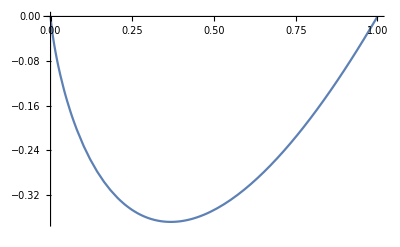

```mathematica
Plot[x Log[x],{x,0,1}]
```

```mathematica
Limit[x Log[x],x->0]
```

0

```mathematica
FindMinimum[x Log[x],{x,0.1}]
```

{-0.367879,{x→0.367879}}

```mathematica
x/(1-x) Log[x]/.x->10000//N
```

-9.21126

```mathematica
Log[1/x]/.x->10000//N
```

-9.21034

## Casas-Ibarra results - study on λ_6

Input Parameters

## SM

```mathematica
v = 2.46220569 10^2;
```

## PMNS Matrix

```mathematica
PMNS={{1, 0, 0}, {0, Cos[θ23], Sin[θ23]}, {0, -Sin[θ23], Cos[θ23]}}.{{Cos[θ13], 0, Sin[θ13] ⅇ^(-ⅈ δCP)}, {0, 1, 0}, {-Sin[θ13] ⅇ^(+ⅈ δCP), 0, Cos[θ13]}}.{{Cos[θ12], Sin[θ12], 0}, {-Sin[θ12], Cos[θ12], 0}, {0, 0, 1}};
```

```mathematica
(*PMNS//MatrixForm*)
```

```mathematica
θ12 = 33.62°;
θ12max = θ12+0.78°;
θ12min = θ12-0.76°;
```

```mathematica
θ23 = 47.2°;
θ23max = θ23+1.9°;
θ23min = θ23-3.9°;
```

```mathematica
θ13 = 8.54°;
θ13max = θ13+0.15°;
θ13min = θ13-0.15°;
```

```mathematica
(*δCP = 234°;
δCPmax = δCP+43°;
δCPmin = δCP-31°;*)
```

```mathematica
δCP = 0°;
```

## Neutrino mass splitting

```mathematica
m1=0;
```

```mathematica
m2=√(7.53 10^-5);
Δm2 = √2 0.18 10^-5/m2;
```

```mathematica
m3=√(2.44 10^-3+m2^2);
Δm3 = √2 0.06 10^-3/m3;
```

```mathematica
Dnu={{m1, 0, 0}, {0, m2, 0}, {0, 0, m3}}*10^-9;
```

## Casas-Ibarra Function

```mathematica
CI[λ4_,λ5_,Mψ_,mψψ_,m2ϕ_]:=Block[{M0,eigenM0,UCHI,eigenS0,US,M0nu,eigenM0nu,UM,DMminusonehalf,ROT,λ6},
M0 = {{Mψ, (v λ5)/(√2), (v λ4)/(√2)}, {(v λ5)/(√2), 0, mψψ}, { (v λ4)/(√2), mψψ, 0}};
{eigenM0,UCHI}=Eigensystem[M0];
{eigenS0,US}=Eigensystem[m2ϕ];
M0nu=Table[1/(32 π^2)Sum[US⟦l,i⟧US⟦l,j⟧ Sum[(UCHI⟦k,3⟧*)^2 (eigenM0⟦k⟧^3/(eigenS0⟦l⟧-eigenM0⟦k⟧^2))Log[eigenM0⟦k⟧^2/eigenS0⟦l⟧],{k,1,3}],{l,1,2}],{i,1,2},{j,1,2}];
{eigenM0nu,UM}=Eigensystem[M0nu];
DMminusonehalf = DiagonalMatrix[1/√Abs[eigenM0nu]];
ROT[θ_]:={{0, Cos[θ], -Sin[θ]}, {0, Sin[θ], Cos[θ]}};

λ6[θ_]:=(UMᵀ.DMminusonehalf.ROT[θ].√Dnu.PMNS†)ᵀ//FullSimplify;
λ6[0](*//MatrixForm*)
];
```

Scalar DM (m_η << m_χ)

## M_Ψ >> M_ψψ'

### Inputs

```mathematica
v = 2.46220569 10^2;
```

```mathematica
lambda4Input=10^-10;
lambda5Input =10^-10;
```

```mathematica
mCPsiInput=10^5;
mpsipsipInput=10^3;
```

```mathematica
MPHI2 = {{10^1,0},{0,10^1}}^2;
```

### Result

```mathematica
CI[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2]//MatrixForm
```

(-6.72089 | 4.38211
-6.20435 | 21.4117
8.18549 | 19.8275)

## M_ψψ'>>M_Ψ

### Inputs

```mathematica
v = 2.46220569 10^2;
```

```mathematica
lambda4Input=10^-10;
lambda5Input =10^-10;
```

```mathematica
mCPsiInput=10^3;
mpsipsipInput=10^5;
```

```mathematica
MPHI2 = {{10^1,0},{0,10^1}}^2;
```

### Result

```mathematica
CI[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2]//MatrixForm
```

(0.346436 | 0.531333
1.69274 | 0.490497
1.5675 | -0.64712)

## M_ψψ'=M_Ψ = M

### Inputs

```mathematica
v = 2.46220569 10^2;
```

```mathematica
lambda4Input=10^-5;
lambda5Input =10^-5;
```

```mathematica
mCPsiInput=10^4;
mpsipsipInput=10^4;
```

```mathematica
MPHI2 = {{10^2,0},{0,10^2}}^2;
```

### Result

```mathematica
CI[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2]//MatrixForm
```

(0.83412 | 1.2793
4.07565 | 1.18098
3.77409 | -1.55808)

Fermion DM (m_χ << m_η)

## M_Ψ >> M_ψψ'

### Inputs

```mathematica
v = 2.46220569 10^2;
```

```mathematica
lambda4Input=10^-5;
lambda5Input =10^-5;
```

```mathematica
mCPsiInput=10^4;
mpsipsipInput=10^2;
```

```mathematica
MPHI2 = {{10^5,0},{0,10^5}}^2;
```

### Result

```mathematica
CI[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2]//MatrixForm
```

(4.92949 | 7.56042
24.0863 | 6.97935
22.3042 | -9.20796)

## M_ψψ'>>M_Ψ

### Inputs

```mathematica
v = 2.46220569 10^2;
```

```mathematica
lambda4Input=10^-5;
lambda5Input =10^-5;
```

```mathematica
mCPsiInput=10^2;
mpsipsipInput=10^4;
```

```mathematica
MPHI2 = {{10^5,0},{0,10^5}}^2;
```

### Result

```mathematica
CI[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2]//MatrixForm
```

(3.79798 | 5.82501
18.5576 | 5.37732
17.1845 | -7.09438)

## M_ψψ'=M_Ψ = M

### Inputs

```mathematica
v = 2.46220569 10^2;
```

```mathematica
lambda4Input=10^-5;
lambda5Input =10^-5;
```

```mathematica
mCPsiInput=10^3;
mpsipsipInput=10^3;
```

```mathematica
MPHI2 = {{10^5,0},{0,10^5}}^2;
```

### Result

```mathematica
CI[lambda4Input,lambda5Input,mCPsiInput,mpsipsipInput,MPHI2]//MatrixForm
```

(7.13243 | 10.9391
34.8502 | 10.0984
32.2716 | -13.3229)